# Computational Physics Laboratory: Tree Level Gluon Scattering

## Implementation

## Generating Diagrams with 3 and 4 point vertices

```mathematica
grafobase = {{1,-1},{2,-1},{3,-1}}; (*Skeleton digrams*)
(* Take a graph and generate a list of graphs obtained by splitting each line into 3,the number of external points and vertices of the starting graph must be known*)
inserzione3[grafo_]:=Module[{nuovigrafi,indici,npt,nvert},
indici = Flatten[grafo]; (*Convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
nuovigrafi = Table[inserisci3[i,npt+1,nvert-1,grafo], (*insert a new point npt+1 and a new vertex nvert-1*)
{i,1,Length[grafo]} (*Length[grafo] gives the numbers of pairs of grafo = number of lines*)
];
Return[nuovigrafi]
]
(*Take a line and split it in 3*)
inserisci3[pos_,ext_,int_,grafo_]:=Module[{temp,pippo},
 (*remove a line and replace it with 3 lines*)
temp = ReplacePart[grafo,
pippo[ {ext,int}(*external point connected to the vertex*) , {grafo[[pos,1]](*substituted coordinate*),int} , {grafo[[pos,2]],int}],
pos]; (*substitute the pos-th element*)
temp =temp/.{pippo->Sequence}; (*1 -> 3 is not an admissible operation, use the wrapper pippo *)
(*Sequence is the argument of the container,it permits us to open the box without further manipulation*)
Return[temp]
]

(*Add 4 point vertex*)
inserzione4[grafo_]:=Module[{indici,npt,nvert,nuovigrafi},
indici = Flatten[grafo]; (*convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
nuovigrafi = Table[inserisci4[i,npt+1,grafo], (*insert a new point npt+1 in grafo*)
{i,-1,nvert,-1} (*loop over the vertives, from -1 to n vert with steps of -1*)
];
Return[nuovigrafi]
]

inserisci4[vertice_,ext_,grafo_]:=If[
Count[grafo,vertice,2]===3, (*Count searches a pattern (the vertices) inside grafo and searches at level 2*)
Append[grafo,{ext,vertice}],(* if the condition is verified, i.e it's a 3 point vertex, then add a new line from the vertex to the external point*)
{}(*otherwise do nothing*)
]

(*generate graphs from a skeleton graph *)
generagrafi[n_]:=Module[{listagrafi,nuovigrafi3,nuovigrafi4,i},
i=3;
listagrafi = {grafobase};
While[i<n,
nuovigrafi3 = Map[inserzione3,listagrafi]; (*vectorized*)
nuovigrafi3 = Flatten[nuovigrafi3,1];
nuovigrafi4=Map[inserzione4,listagrafi];
nuovigrafi4 = Flatten[nuovigrafi4,1];
listagrafi = Join[nuovigrafi3,nuovigrafi4];
listagrafi = DeleteCases[listagrafi,{}];
++i;
];
Return[listagrafi]
]
generagrafi3[n_]:=Module[{listagrafi,nuovigrafi3,i},
i=3;
listagrafi = {grafobase};
While[i<n,
nuovigrafi3 = Map[inserzione3,listagrafi]; 
nuovigrafi3 = Flatten[nuovigrafi3,1];
listagrafi = Join[nuovigrafi3];
++i;
];
Return[listagrafi]
]
listaimpulsi[grafo_]:=Map[Apply[p,#]&,grafo]
generaequazioni[grafo_]:=Module[{indici,npt,nvert,impulsi,equazioni,impulsivertice,impulsiinterni,eq,incognite,globale},
indici = Flatten[grafo]; 
npt = Max[indici];
nvert = Min[indici];

impulsi = listaimpulsi[grafo];
(*List of equation of the vertices, note that all momenta are entering!*)
equazioni=Table[
(*Cases searches a recurrence inside the list impulsi*)
impulsivertice = Join[Cases[impulsi,p[_,i]],
				   -Cases[impulsi,p[i,_]] (* exiting momenta need a -*)
];
eq=Apply[Plus,impulsivertice] ==0; (*solve momentum conservation*)
eq,
{i,-1,nvert,-1}
];
(*redefine equations, if in the equation i find p[i,j] with i>0, substitute with p[i]*)
(*/; is an if, the pattern is recognized if i>0*)
equazioni=equazioni/.p[i_/;i>0,j_]:>p[i];incognite = Cases[equazioni,p[_,_],Infinity]; (*equations with p[_,_] 2 indices are internal momenta, Infinity makes it search the whole list*)
globale = Rule[p[npt],-Sum[p[k],{k,1,npt-1}]]; (*The last momentum is fixed by global momentum conservation*)
equazioni = equazioni/. globale;
(*Solve the linear system of equations*)
impulsiinterni=Solve[equazioni,incognite];

Return[impulsiinterni]

];
Diagrams[grafo_]:= Module[{impulsiinterni,nvert},
nvert = Min[Flatten[grafo]];
regole=generaequazioni[grafo];(*gives the momenta*)
(*Identify vertices and external lines, vertices have in common 3,4 identical negatives indices *)
interne = Cases[grafo,{i_/;i<0,j_/;j<0}]; (*Seleziono solo gli impulsi*)
impulsiinterni=listaimpulsi[interne]/.regole[[1]];
(*give them their name, [[1]] takes the first solution*)
propagatori=Table[
Prop[impulsiinterni[[i]],interne[[i]]//. {a_/; a<0,b_}:>{mu[a,b],mu[b,a]},interne[[i]]//. {a_/; a<0,b_}:>{c[a,b],c[b,a]}] ,
{i,1,Length[interne]}];
propagatori=Apply[Times,propagatori]; 
vertici= Table[
impulsi=listaimpulsi[grafo];
impulsivertice = Join[Cases[impulsi,p[_,i]],-Cases[impulsi,p[i,_]]];(*Impulsi tutti entranti*)
indicivertice= impulsivertice//. -p[i,j_]:>mu[j,i] //.p[j_/;j>0,i]:> mu[j]//.p[j_/;j<0,i]:> mu[j,i];(*from the momenta we can get Lorentz indices*)
colorevertice= impulsivertice//. -p[i,j_]:>c[j,i] //.p[j_/;j>0,i]:> c[j]//.p[j_/;j<0,i]:> c[j,i];
(*same for colors*)
impulsivertice=impulsivertice/.regole[[1]]/.p[i_/;i>0,j_]:>p[i];(*substiture internal momenta and external momenta with 1 index*)
vertice = V[i][impulsivertice,indicivertice,colorevertice];(*The i-th vertex depend on momenta, lorentz indices and color indices*)
vertice
,
{i,-1,nvert,-1}];
vertici =Apply[Times,vertici];
Return[Times[vertici,propagatori]]
]

(*diagrams with n external points and only 3 and 4 point vertices*)
generatediagrams[n_]:= Module[{temp,grafi,diagrammi},
grafi = generagrafi[n];
diagrammi=Map[Diagrams,grafi];
Return[diagrammi]
]
(*diagrams with n external points and only 3 point vertices*)
generatediagrams3[n_]:= Module[{temp,grafi,diagrammi},
grafi = generagrafi3[n];
diagrammi=Map[Diagrams,grafi];
Return[diagrammi]
]

masterInsert[grafo_]:=Module[{nuovigrafi,indici,npt,nvert},
indici = Flatten[grafo]; (*Convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
pos=Position[grafo,{npt,nvert}]//Max;
If[Count[grafo,nvert,2]===3,
nuovigrafi=List[inserisci3[pos,npt+1,nvert-1,grafo],inserisci4[nvert,npt+1,grafo]],
nuovigrafi=List[inserisci3[pos,npt+1,nvert-1,grafo]]
];
Return[nuovigrafi]
]
(*generate only graphs which contribute to f[c1,c2,a1]f[c3,a2,a1]f[c4,a3,a2]f[c5,a4,a3]...f[c_n,c_n-1,a_n-3]*)
generatemastergraph[n_]:=Module[{mastergraphs,i},
i=3;
mastergraphs = {grafobase};
While[i<n,
mastergraphs = Map[masterInsert,mastergraphs]; (*vectorized*)
mastergraphs = Flatten[mastergraphs,1];
++i;
];
Return[mastergraphs]
]
(*generate only graphs which contribute to f[c1,c2,a1]f[c3,a2,a1]f[c4,a3,a2]f[c5,a4,a3]...f[c_n,c_n-1,a_n-3]*)
generatemasterdiagrams[n_]:= Module[{temp,grafi,diagrammi},
grafi = generatemastergraph[n];
diagrammi=Map[Diagrams,grafi];
Return[diagrammi]
]
```

## Propagator (Axial gauge)

-Graphics-

-Graphics-

External gluons are physical gluons and gauge trasformation  leaves the physics unchanged, so we can choose a gauge for each of them

```mathematica
polsum[p[i_],{mu1_,mu2_}]:= (SP[{mu1},{mu2}]-1/SP[p[i],n[i]](SP[p[i],{mu1}]SP[n[i],{mu2}]+SP[p[i],{mu2}]SP[n[i],{mu1}]));
```

```mathematica
(*Feynman Gauge*)
```

```mathematica
gluon=Prop[p_,{mu1_,mu2_},{c1_,c2_}]:>-I myDelta[c1,c2]gprop[p,mu1,mu2];
propColorOnly=Prop[p_,{mu1_,mu2_},{c1_,c2_}]:>myDelta[c1,c2];
```

```mathematica
propagator[p_,mu1_,mu2_]:=SP[{mu1},{mu2}]/SP[p,p];
```

## Vertices

-Graphics-

```mathematica
V3p[{p1_,p2_,p3_},{mu1_,mu2_,mu3_}]:=SP[p1-p2,{mu3}]SP[{mu1},{mu2}] +SP[p2-p3,{mu1}]SP[{mu2},{mu3}]+SP[p3-p1,{mu2}]SP[{mu3},{mu1}];

(*Factorize color and Lorentz*)
V3QCD=V[i_][{p1_,p2_,p3_},{mu1_,mu2_,mu3_},{c1_,c2_,c3_}]:>-Subscript[g, s]f[c1,c2,c3]V3Lorentz[{p1,p2,p3},{mu1,mu2,mu3}];
V3ColorOnly=V[i_][{p1_,p2_,p3_},{mu1_,mu2_,mu3_},{c1_,c2_,c3_}]:>f[c1,c2,c3];
```

-Graphics-

```mathematica
V4QCD=V[i_][{p1_,p2_,p3_,p4_},{mu1_,mu2_,mu3_,mu4_},{c1_,c2_,c3_,c4_}]:>-I Subscript[g, s]^2(
f[c1,c2,c[x,i]]f[c3,c4,c[x,i]] (SP[{mu1},{mu3}]SP[{mu2},{mu4}]-SP[{mu1},{mu4}]SP[{mu2},{mu3}])-
f[c1,c3,c[x,i]]f[c2,c4,c[x,i]](SP[{mu1},{mu4}]SP[{mu2},{mu3}]-SP[{mu1},{mu2}]SP[{mu3},{mu4}])+
f[c1,c4,c[x,i]]f[c2,c3,c[x,i]](SP[{mu1},{mu2}]SP[{mu3},{mu4}]-SP[{mu1},{mu3}]SP[{mu2},{mu4}])
);
```

## Metric Tensor

```mathematica
(*4 momentum properties*)
SetAttributes[SP,Orderless]
Contract = (#//.{
SP[a_,{mu_}]SP[b_,{mu_}]:>SP[a,b], (*Contraction*)
SP[p_,{mu_}]SP[p_,{mu_}]:> SP[p,p],(*Square*)
SP[a_Integer *p_,{mu_}]:> a SP[p,{mu}],(*Homogeneity*)
SP[a_Integer *p_,q_]:> a SP[p,q], (*Homogeneity*)
SP[p_+q_,{mu_}]:>SP[p,{mu}]+SP[q,{mu}] ,(*Linearity*)
SP[a_,b_+c_]:>(SP[a,b]+SP[a,c]),(*Distributive Property*)
SP[{mu_},{mu_}]:> 4 (*Trace*),
SP[n,n]:>0 (*Light Cone Gauge*),
 SP[p[i_],p[i_]]:>0 (*On Shell Condition*)
})&;
Pcons[n_]:=#/.p[1]->-Sum[p[i],{i,2,n}] &
Physpol=(#//. SP[eps[i_],p[i_]]:>0)&;
```

## Color Algebra

```mathematica
antisymf=#//.{(*when there are repeated indices*)
f[i1_,i2_,i3_]/;(i1===i2||i1===i3||i2===i3):>0,
(*Order in decreasing alphanumerical order*)
f[i1_,i2_,i3_]:>Module[{perm,sorted},
perm=Reverse[Ordering[{i1,i2,i3}]];(*gives the permutation needed to reorder*)
sorted={i1,i2,i3}[[perm]]; (*the list is reordered according to perm*)
Signature[perm]*f@@sorted]}&;
```

```mathematica
(*frule: A function that takes an expression with color structures,renames repeated indices as a[1],a[2],...
When there are more than 2 repeated indices,the ambiguity in deciding
which becomes a[1] and which a[2] is resolved using the criterion
that a[1] is assigned to the f[c[i],c[j],x]
for which the product and sum {i·j, i+j} is smaller.e.g f[c[1],c[2],x]f[c[3],c[4],y]f[c[5],x,y]---> f[c[1],c[2],a[1]]f[c[3],c[4],a[2]]f[c[5],a[1],a[2]]*)

frule[expr_]:=Module[{terms,processProduct,processedTerms},
(*Support function that processes products of f[a_,b_,c_]*)
processProduct[prod_Times]:=Module[{fs,allIndices,counts,repeated,repList,repMap,products,sum,repSet,repWithVals,candidateFs,transformedArgs,sortedRep},
fs=Cases[List@@prod,f[__],{1}];(*The product becomes a list,and I isolate the f's*)
allIndices=Flatten[fs/. f[args__]:>{args}];(*List with the arguments of f*)
counts=Tally[allIndices];(*Count how many indices:{x,2},{y,2},{c[1],1},..*)
repeated=Select[counts,#[[2]]>1&];(*Keep only repeated indices*)
repList=repeated[[All,1]];(*Extract the first element from all {x,y,...}*)
repSet=AssociationThread[repList->ConstantArray[True,Length[repList]]];(*Create a key-value map to track which are the repeated indices,x->True,y->True,... *)
repWithVals=Map[Function[indx,(*Select the candidate f's with exactly one repeated index*)candidateFs=Select[fs,MemberQ[List@@#,indx]&&Count[List@@#,_?(KeyExistsQ[repSet,#]&)]==1&];
transformedArgs=List@@#/. c[x_]:>x&/@candidateFs;
(*Calculate the product and sum of the indices of c[i]*)
products=Times@@DeleteCases[#,indx]&/@transformedArgs;
sum=Plus@@DeleteCases[#,indx]&/@transformedArgs;
{indx,{Min[products],Min[sum]}}],
repList];
(*Sort based on the calculated values*)
sortedRep=SortBy[repWithVals,Last];
	(*Create the map for repeated index->a[idx] according to value order*)
repMap=Association[MapIndexed[#1[[1]]->a[First[#2]]&,sortedRep]];
	(* Repeated index->mute index a[i]*)
	prod/. f[args__]:>f@@(Replace[{x_:>If[KeyExistsQ[repMap,x],repMap[x],x]}]/@{args})];

(*If expr is a sum,then act on each subterm,otherwise act directly*)
terms=If[Head[expr]===Plus,List@@expr,{expr}];
(*Execute for each term of expr*)processedTerms=terms/. term_:>term/. {prod_Times/;Length[Cases[prod,f[__],{1}]]>=1:>processProduct[prod],f[__]:>processProduct[f[__]]};
(*Reorder in descending order*)
processedTerms=processedTerms//antisymf;
(*Recombine into the original sum or return the single term*)
If[Length[processedTerms]==1,First[processedTerms],Plus@@processedTerms]
]
```

```mathematica
ClearAll[myDelta]
SetAttributes[myDelta,Orderless]
ColorDelta=#//.{
myDelta[a_,b_]myDelta[a_,b_]:>(Nc^2-1) ,(*same argument*)
myDelta[a_,a_]:>(Nc^2-1),(*Trace*)
myDelta[a_,b_]*expr_:>(expr/. b->a),
c[i_,j_]:> aa[i,j]}&;
```

Jacobi Identity

-Graphics-

```mathematica
Jacobi = (#/.f[c[3],c[2],e_]f[c[4],c[1],e_]:>f[c[4],c[2],e]f[c[3],c[1],e]-f[c[2],c[1],e] f[c[4],c[3],e] )&;
```

```mathematica
Mandelstam=(#/.
{SP[p[1],p[2]]->s/2,
SP[p[3],p[4]]->s/2,
SP[p[1],p[3]]->t/2,
SP[p[2],p[4]]->t/2,
SP[p[1],p[4]]->u/2,
SP[p[2],p[3]]->u/2})&;
```

```mathematica
(*Invariants*)
s[i_,j_]/;i>j:=s[j,i]  (*Simmetry s[i,j]=s[j,i]*)
vars=Table[s[i,j],{i,1,4},{j,i+1,5}]//Flatten;
relations=Table[Sum[s[i,j],{j,1,5}]-s[i,i]==0,{i,1,5}];(*momentum conservation*)
basis={s[1,2],s[1,3],s[1,4],s[2,3],s[2,4]};(*choose a basis*)
constraint5=Solve[relations,Complement[vars,basis]]//Flatten;
dependentVars=Complement[vars,basis];
mtable=Table[SP[p[i],p[j]],{i,1,5},{j,i+1,5}];
Mandelstam5Full =  #/.Flatten[Table[mtable[[i,j]]->1/2 s[i,j+i],{i,1,5},{j,1,5-i}]]&;
Mandelstam5= (#//Mandelstam5Full)/.constraint5&;
TableForm[Table[{depVar,depVar/. constraint5},{depVar,dependentVars}],TableHeadings->{None,{"Variable","Expression in basis"}}]
reverseMandelstam=Flatten[Table[s[i,j+i]->2mtable[[i,j]],{i,1,5},{j,1,5-i}]];
```

Variable | Expression in basis
s[1,5] | -s[1,2]-s[1,3]-s[1,4]
s[2,5] | -s[1,2]-s[2,3]-s[2,4]
s[3,4] | -s[1,2]-s[1,3]-s[1,4]-s[2,3]-s[2,4]
s[3,5] | s[1,2]+s[1,4]+s[2,4]
s[4,5] | s[1,2]+s[1,3]+s[2,3]

-Graphics-

```mathematica
fcolor=(#//.{ 
f[a_,c_,d_] f[b_,c_,d_]:>Nc myDelta[a,b],
f[c_,a_,d_] f[c_,b_,d_]:>Nc myDelta[a,b],
f[c_,a_,d_] f[b_,c_,d_]:>-Nc myDelta[a,b],
f[a_,c_,d_] f[b_,c_,d_]:>-Nc myDelta[a,b],

f[c_,d_,a_] f[c_,d_,b_]:>Nc myDelta[a,b],
f[a_,d_,c_] f[b_,d_,c_]:>+Nc myDelta[a,b],
f[a_,d_,c_] f[c_,d_,b_]:>-Nc myDelta[a,b],
f[c_,d_,a_] f[b_,d_,c_]:>-Nc myDelta[a,b],

f[d_,c_,a_] f[d_,c_,b_]:>Nc myDelta[a,b],
f[d_,a_,c_] f[d_,b_,c_]:>Nc myDelta[a,b],
f[d_,c_,a_] f[d_,b_,c_]:>-Nc myDelta[a,b],
f[d_,a_,c_] f[d_,c_,b_]:>-Nc myDelta[a,b],

f[c_,a_,b_]f[c_,a_,b_]:> Nc (Nc^2-1),

f[a_,b_,e_]f[c_,d_,e_]f[a_,b_,g_] f[c_,d_,g_]:>Nc^2(Nc^2-1),

f[a_,b_,e_]f[c_,d_,e_]f[a_,b_,g_] f[c_,d_,g_]:>Nc^2(Nc^2-1),

f[e_,a_,b_]f[c_,e_,d_]f[g_,a_,d_]f[g_,c_,b_]:>-Nc^2/2(Nc^2-1),
f[e_,a_,b_]f[e_,c_,d_]f[g_,a_,d_]f[g_,c_,b_]:>Nc^2/2(Nc^2-1),
f[a_,e_,b_]f[c_,e_,d_]f[g_,a_,d_]f[g_,c_,b_]:>Nc^2/2(Nc^2-1),
myDelta[a_,b_]myDelta[a_,b_]:> Nc^2-1
})&;
```

```mathematica
csub = #/.{
f[a_,b_,c_]f[d_,b_,g_]f[g_,h_,a_]f[e_,f_,c_]f[j_,d_,e_]f[h_,j_,f_]:> Nc^3/4(Nc^2-1),
f[c1_,b2_,b1_]f[c3_,a2_,a1_] f[c3_,c2_,b1_]f[c4_,c1_,a1_]f[c5_,c2_,a2_]f[c5_,c4_,b2_]->Nc^3/4(Nc^2-1),
f[c1_,b2_,b1_]f[c2_,a2_,a1_]f[c3_,c2_,b1_]f[c4_,c1_,a1_] f[c5_,c3_,a2_]f[c5_,c4_,b2_]->-Nc^3/4(Nc^2-1),
f[c1_,b2_,b1_]f[c1_,a2_,a1_]f[c3_,c2_,b1_] f[c4_,c2_,a1_]f[c5_,c3_,a2_]f[c5_,c4_,b2_]->0,
f[c2_,b2_,b1_]f[c3_,a2_,a1_]f[c3_,c1_,b1_]f[c4_,c1_,a1_]f[c5_,c2_,a2_]f[c5_,c4_,b2_]->Nc^3/4(Nc^2-1),
f[c1_,a2_,a1_]f[c2_,c1_,b1_]f[c3_,b2_,b1_]f[c4_,c2_,a1_]f[c5_,c3_,a2_]f[c5_,c4_,b2_]->-Nc^3/4(Nc^2-1),
f[c1_,a2_,a1_]f[c3_,b2_,b1_]f[c4_,c1_,b1_]f[c4_,c2_,a1_]f[c5_,c2_,b2_]f[c5_,c3_,a2_]->Nc^3/4(Nc^2-1),
f[c1_,b2_,b1_]f[c3_,c1_,a1_]f[c3_,c2_,b1_]f[c4_,c2_,a2_]f[c5_,a2_,a1_]f[c5_,c4_,b2_]->-Nc^3/4(Nc^2-1),
f[c3_,b2_,b1_]f[c3_,c1_,a1_]f[c4_,c1_,b1_]f[c4_,c2_,a2_]f[c5_,a2_,a1_]f[c5_,c2_,b2_]->Nc^3/4(Nc^2-1),
f[c2_,b2_,b1_]f[c3_,c1_,a1_]f[c4_,c1_,b1_]f[c4_,c2_,a2_]f[c5_,a2_,a1_]f[c5_,c3_,b2_]->Nc^3/4(Nc^2-1),
f[c3_,a2_,a1_]f[c3_,b2_,b1_]f[c4_,c1_,b1_]f[c4_,c2_,a2_]f[c5_,c1_,a1_]f[c5_,c2_,b2_]->0,
f[c2_,a2_,a1_]f[c3_,b2_,b1_]f[c4_,c1_,b1_]f[c4_,c3_,a2_]f[c5_,c1_,a1_]f[c5_,c2_,b2_]->-Nc^3/4(Nc^2-1),
f[c2_,b2_,b1_]f[c3_,c2_,a2_]f[c4_,a2_,a1_]f[c4_,c1_,b1_]f[c5_,c1_,a1_]f[c5_,c3_,b2_]->-Nc^3/4(Nc^2-1),
f[c1_,a2_,a1_]f[c2_,b2_,b1_]f[c4_,c1_,b1_]f[c4_,c3_,a2_]f[c5_,c2_,a1_]f[c5_,c3_,b2_]->-Nc^3/4(Nc^2-1),
f[c2_,c1_,a1_]f[c3_,a2_,a1_]f[c3_,c2_,b2_]f[c4_,c1_,b1_]f[c5_,b2_,b1_]f[c5_,c4_,a2_]->-Nc^3/4(Nc^2-1),
f[c2_,c1_,a1_]f[c3_,c2_,b2_]f[c4_,a2_,a1_]f[c4_,c1_,b1_]f[c5_,b2_,b1_]f[c5_,c3_,a2_]->-Nc^3/4(Nc^2-1),
f[c2_,c1_,a1_]f[c3_,c2_,b2_]f[c4_,c1_,b1_]f[c4_,c3_,a2_]f[c5_,a2_,a1_]f[c5_,b2_,b1_]->0,
f[c1_,a2_,a1_]f[c3_,c2_,b2_]f[c4_,c1_,b1_]f[c4_,c3_,a2_]f[c5_,b2_,b1_]f[c5_,c2_,a1_]->-Nc^3/4(Nc^2-1),
f[c1_,b2_,b1_]f[c2_,c1_,a1_]f[c4_,c2_,b1_]f[c4_,c3_,a2_]f[c5_,a2_,a1_]f[c5_,c3_,b2_]->-Nc^3/4(Nc^2-1),
f[c1_,a2_,a1_]f[c2_,c1_,b1_]f[c3_,c2_,a1_]f[c4_,c3_,b2_]f[c5_,b2_,b1_]f[c5_,c4_,a2_]->Nc^3/4(Nc^2-1),
f[c1_,b2_,b1_]f[c2_,a2_,a1_]f[c3_,c1_,a1_]f[c4_,c3_,b2_]f[c5_,c2_,b1_]f[c5_,c4_,a2_]->Nc^3/4(Nc^2-1),
f[c1_,b2_,b1_]f[c2_,c1_,a1_]f[c3_,a2_,a1_]f[c4_,c3_,b2_]f[c5_,c2_,b1_]f[c5_,c4_,a2_]->Nc^3/4(Nc^2-1),
f[c2_,a2_,a1_]f[c3_,b2_,a1_]f[c5_,c2_,b2_]f[c5_,c3_,a2_]-> Nc^2/2(Nc^2-1),
f[c2_,b2_,a1_]f[c4_,c2_,a2_]f[c5_,a2_,a1_]f[c5_,c4_,b2_]-> -Nc^2/2(Nc^2-1),
f[c1_,b2_,a2_]f[c3_,c1_,a1_]f[c5_,a2_,a1_]f[c5_,c3_,b2_]-> Nc^2/2(Nc^2-1),
f[c1_,a2_,a1_]f[c3_,a1_,b1_]f[c4_,c1_,b1_]f[c4_,c3_,a2_]->- Nc^2/2(Nc^2-1),
f[c3_,a2_,a1_]f[c3_,c2_,b2_]f[c5_,b2_,a1_]f[c5_,c2_,a2_]-> Nc^2/2(Nc^2-1)
}&;
```

## Feynman Rules

```mathematica
FeynmanRules=(#/.gluon/. V3QCD/.V4QCD/.gprop->propagator/.V3Lorentz->V3p//ColorDelta//antisymf//Expand)&;
```

## Formatting

```mathematica
Format[SP[p_,{mu_}]]:= Superscript[p,mu]
Format[SP[{mu_},{nu_}]]:=Subscript[η,Row[{mu, nu}]]
Format[SP[p_,q_]]:=p q
Format[mu]=μ;
Format[nu]=ν;
Format[eps]=ϵ;
Format[p[i_]]:=Subscript[p,i]
Format[mu[i_]]:=Subscript[μ,i]
Format[nu[i_]]:=Subscript[ν,i]
Format[c[i_]]:=Subscript[c,i]
Format[c[i_,j_]]:=Subscript[c,i,j]
Format[mu[i_,j_]]:=Subscript[mu,i,j]
Format[nu[i_,j_]]:=Subscript[nu,i,j]
Format[x[i_]]:=Subscript[x,i]
Format[a[i_]]:=Subscript[a,i]
Format[s[i_,j_]]:=Subscript[s,Row[{i, j}]]
Format[v[i_]]:=Subscript[v,i]
Format[b[i_]]:=Subscript[b,i]
Format[eps[i_]]:=Subscript[ϵ,i]
Format[f[c1_,c2_,c3_]]:=Superscript[f,Row[{c1,c2,c3}]]
Format[myDelta[a_,b_]]:= Superscript[δ,Row[{a,b}]]
```

## Color Contractions

```mathematica
Format[tr[a_,b_,c_]]:=Tr[a b c]
Format[T[a_]]:=Superscript[T,a]
Format[T[a_][i_,j_]]:=Subscript[T[a],Row[{i,j}]]
Format[tDelta[i_,j_]]:=Subscript[δ,i,j]
Format[k[i_]]:=Subscript[k,i]
```

```mathematica
Fierz=#//.{T[x_][k[a_],k[b_]]T[x_][k[c_],k[d_]]:> 
1/2(tDelta[a,d]tDelta[b,c] (*- 1/NctDelta[a,b]tDelta[c,d]*)),
(T[x_][k[a_],k[b_]])^2:> Nc^2/2}&;
```

```mathematica
SetAttributes[tDelta,Orderless]
TDelta=#//.{
tDelta[a_,b_]tDelta[a_,b_]:>Nc ,(*Stesso argomento*)
tDelta[a_,a_]:>Nc,(*Traccia*)
tDelta[a_,b_]*tDelta[b_,d_]:>tDelta[a,d]}&;
```

```mathematica
trOrder=#//.{tr[a_,b_,c_]:> tr[b,c,a]/; OrderedQ[{b,a}],
 tr[a_,b_,c_]:> tr[c,a,b]/; OrderedQ[{c,a}]}&;
```

```mathematica
SetAttributes[Color,Listable];
Color[expr_]:=Module[{fs,coeff,terms,processTerm,processedTerms},
(*Convert to traces*)
{coeff,terms}=List@@FactorTerms[expr/. f[a_,b_,c_]:>-2 I (tr[T[a],T[b],T[c]]-tr[T[b],T[a],T[c]]),_Complex];
(*Expand and isolate products of traces*)
terms=List@@Expand[terms];
(* Helper: Process products of traces*)
processTerm[term_]:=Module[{factors,replaced},factors=List@@term;
replaced=MapIndexed[Function[{elem,pos},elem/. tr[T[a_],T[b_],T[c_]]:>T[a][k[3 pos[[1]]-2],k[3 pos[[1]]-1]]*T[b][k[3 pos[[1]]-1],k[3 pos[[1]]]]*T[c][k[3 pos[[1]]],k[3 pos[[1]]-2]]],factors];
(Times@@replaced)//Fierz//Expand//TDelta//Simplify];
(*parallel Map over each term*)
processedTerms=ParallelMap[processTerm,terms];
(* Assemble and Simplify*)
coeff*Simplify[Total[processedTerms]]];
```

```mathematica
products=(generatediagrams3[5]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x;
```

```mathematica
prodotti=Table[(products[[i]]/.a->b)products[[j]],{i,1,15},{j,1,15}];
```

```mathematica
(prodotti[[1]]//Color)/.Nc^3 (-1+Nc^2)->k/.-Nc^3 +Nc^5->k//AbsoluteTiming
```

{5.12118,{k,-k/2,k/2,k/4,-k/4,-k/4,k/2,k/4,-k/4,0,k/4,0,-k/2,-k/4,k/4}}

```mathematica
(prodotti[[1]]//fcolor//ColorDelta//fcolor//csub)/.Nc^3 (-1+Nc^2)->k//AbsoluteTiming
```

{0.045855,{k,-k/2,k/2,k/4,-k/4,-k/4,k/2,k/4,-k/4,0,k/4,0,-k/2,-k/4,k/4}}

## Verifying Ward Identities

## Jacobi Relations

-Graphics-

```mathematica
jacobiIdentity[a_,b_,c_,d_,e_]:=antisymf[f[a,b,e]] antisymf[f[e,c,d]]+antisymf[f[b,c,e]] antisymf[f[e,a,d]]+antisymf[f[c,a,e]] antisymf[f[e,b,d]];

(*Gives a list of indices*)
getIndices[product_]:=Flatten[List@@product/. f->List];
(*GIves a list of contracted indices*)
findContractedIndices[product_]:=Module[{inds=getIndices[product],counts},
counts=Tally[inds];
Select[counts,Last[#]>1&][[All,1]]
];

generateJacobiRelations[prod_]:=Module[{factors,relations={},contracted=findContractedIndices[prod],pairs,a,b,c,d,e,jacobiExpr,remainingFs,ind1,ind2,pos1,pos2,perm1,perm2,ind1rot,ind2rot,e1,e2},factors=List@@prod;
Do[pairs=Select[Subsets[Range[Length[factors]],{2}],And@@(MemberQ[getIndices[factors[[#]]],e]&)/@#&];
Do[ind1=getIndices[factors[[pair[[1]]]]];
ind2=getIndices[factors[[pair[[2]]]]];
pos1=First@First@Position[ind1,e];
pos2=First@First@Position[ind2,e];
perm1=RotateRight[Range[3],3-pos1];
perm2=RotateRight[Range[3],1-pos2];
ind1rot=ind1[[perm1]];
ind2rot=ind2[[perm2]];
{a,b,e1}=ind1rot;
{e2,c,d}=ind2rot;
If[e1===e2===e,jacobiExpr=jacobiIdentity[a,b,c,d,e];
(*Multiply by the remaining f*)
remainingFs=Times@@factors[[Complement[Range[Length[factors]],pair]]];
jacobiFull=jacobiExpr*remainingFs;
jacobiCanonical=jacobiFull//antisymf//Expand//frule;
AppendTo[relations,jacobiCanonical];],{pair,pairs}],{e,contracted}];
relations]
exprToVector[expr_,canonicalList_]:=Module[{coeffs},coeffs=Table[Simplify[Coefficient[expr,canonicalList[[i]]]],{i,Length[canonicalList]}];
coeffs];
vectorToExpr[vec_,canonicalList_]:=Total[MapThread[#1*#2&,{vec,canonicalList}]]
(*Generate jacobi rules*)
jacobirules[ff_,n_]:= Module[{allRelations,rule,eq,rem,soljacobi},
rule=#/.MapIndexed[#1->v[First[#2]]&,ff]&;
allRelations=Flatten[Map[generateJacobiRelations,ff]]//DeleteDuplicates;
eq=#==0&/@ rule/@allRelations;
rem= #/.{ f[c[1],_a,_a]:>0,f[c[n],_a,_a]:>0,f[c[n],c[1],_]:>0,f[a_,a_,a_]:>0}&;
soljacobi=Flatten[Solve[eq,DeleteCases[rule[ff-(ff//rem)],0]]];
Return[soljacobi/.v[i_]:>ff[[i]]];
]
```

## Ward Identity 2 -> 2

```mathematica
WardId[ngluoni_]:= Module[{ward,Ampiezza,colorsubstructures},
ext=Table[Product[SP[p[i],{mu[i]}],{i,1,j}]Product[SP[eps[i],{mu[i]}],{i,j+1,ngluoni}],{j,1,ngluoni}]//Reverse;
Ampiezza = Total[generatediagrams[ngluoni]]//FeynmanRules//Jacobi//frule; (*Generate the amplitude and use Jacobi*)
colorsubstructures=Apply[List,Collect[Ampiezza , _f]];(*Isolate the gauge invariant substructures*)
(* Jacobi (independent structure constant), Global momentum conservation and physical polarization are necessary conditions to verify Ward's Identity in QCD*)
For[i=1,i<=ngluoni,i++,
Print["Contracting with: ", ext[[i]]];
ward= colorsubstructures[[1]] ext[[i]]//Pcons[ngluoni] //Expand//Contract//Physpol//AbsoluteTiming;
Print["Memory (Mb) before Simplify :" , (ward[[2]]//ByteCount)/1000000.];
ward= ward//Simplify;
Print["Time taken : ",ward];
]
]
```

```mathematica
WardId[4]
```

Contracting with: p_1^μ_1 p_2^μ_2 p_3^μ_3 p_4^μ_4

Memory (Mb) before Simplify :0.033952

Time taken : {0.005832,0}

Contracting with: ϵ_4^μ_4 p_1^μ_1 p_2^μ_2 p_3^μ_3

Memory (Mb) before Simplify :0.035776

Time taken : {0.006852,0}

Contracting with: ϵ_3^μ_3 ϵ_4^μ_4 p_1^μ_1 p_2^μ_2

Memory (Mb) before Simplify :0.039672

Time taken : {0.00762,0}

Contracting with: ϵ_2^μ_2 ϵ_3^μ_3 ϵ_4^μ_4 p_1^μ_1

Memory (Mb) before Simplify :0.040584

Time taken : {0.008014,0}

## Ward Identity 2 -> 3

Isolate color substractures and find independent ones

```mathematica
products=(generatediagrams3[5]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x//Sort;
rule=#/.MapIndexed[#1->v[First[#2]]&,products]&;
allRelations=Flatten[Map[generateJacobiRelations,products]]//DeleteDuplicates;
eq=#==0&/@ rule/@allRelations;
rem= #/.{ f[c[1],_a,_a]:>0,f[c[5],_a,_a]:>0,f[c[5],c[1],_]:>0}&;
soljacobi=Flatten[Solve[eq,DeleteCases[rule[products-(products//rem)],0]]];
(*Convert jacobi relations into a vector form by choosing a basis of structure constant*)
relationVectors=exprToVector[#,products]&/@allRelations;
basisVectors=NullSpace[relationVectors];
BasisVectors=vectorToExpr[#,products]&/@basisVectors;
basisDim=Length[basisVectors]
```

6

```mathematica
lis5=List@@Collect[generatediagrams[5]//Total//FeynmanRules//frule //Contract,products];
```

```mathematica
(lis5//rule)[[All,-1]](*Not ordered according to the basis*)
```

{v_15,v_14,v_13,v_9,v_11,v_1,v_12,v_2,v_10,v_3,v_8,v_4,v_5,v_7,v_6}

```mathematica
permut=Ordering[(lis5//rule)[[All,-1]]];
coeff= (lis5//rule)/(lis5//rule)[[All,-1]];
coeff=coeff[[permut]];(*reoder according to the basis order*)
```

```mathematica
canon=Table[Table[KroneckerDelta[i,j],{j,1,15}],{i,1,15}];
fnellabase= Table[Table[canon[[i]].basisVectors[[j]],{j,1,6}],{i,1,15}];
mext5=Table[Product[SP[p[i],{mu[i]}],{i,1,j}]Product[SP[eps[i],{mu[i]}],{i,j+1,5}],{j,1,5}];
```

```mathematica
Table[(coeff.fnellabase)[[j]]mext5[[5]] //Expand//Contract//Simplify,{j,1,6}]//AbsoluteTiming
Table[(coeff.fnellabase)[[j]]mext5[[4]]//Expand//Contract//Pcons[5]//Contract//Physpol//Simplify,{j,1,6}]//AbsoluteTiming
Table[(coeff.fnellabase)[[j]]mext5[[3]]//Expand//Contract//Pcons[5]//Contract//Physpol//Simplify,{j,1,6}]//AbsoluteTiming
Table[(coeff.fnellabase)[[j]]mext5[[2]]//Expand//Contract//Pcons[5]//Contract//Physpol//Simplify,{j,1,6}]//AbsoluteTiming
Table[(coeff.fnellabase)[[j]]mext5[[1]]//Expand//Contract//Pcons[5]//Contract//Physpol//Simplify,{j,1,6}]//AbsoluteTiming
```

{0.54597,{0,0,0,0,0,0}}

{0.86789,{0,0,0,0,0,0}}

{1.37029,{0,0,0,0,0,0}}

{2.05854,{0,0,0,0,0,0}}

{3.44003,{0,0,0,0,0,0}}

As in the 2 to 2 case, all 15 dependent substructure are 0 when fully contracted with external momenta

```mathematica
((lis5/products)mext5[[5]]//Expand//Contract//Mandelstam5)//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
amp5=List@@Collect[((lis5//rule//Total)//.soljacobi),_v];
```

```mathematica
coff=amp5[[All,-1]]
```

{v_8,v_9,v_10,v_11,v_13,v_14}

```mathematica
(amp5/coff) mext5[[5]]//Expand//Contract//Simplify//AbsoluteTiming
(amp5/coff) mext5[[4]]//Expand//Contract//Physpol//Pcons[5]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
(amp5/coff)mext5[[3]] //Expand//Contract//Physpol//Pcons[5]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
(amp5/coff) mext5[[2]]//Expand//Contract//Physpol//Pcons[5]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
(amp5/coff) mext5[[1]]//Expand//Contract//Physpol//Pcons[5]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
```

{0.499919,{0,0,0,0,0,0}}

{0.851508,{0,0,0,0,0,0}}

{1.26097,{0,0,0,0,0,0}}

{1.69833,{0,0,0,0,0,0}}

{2.74863,{0,0,0,0,0,0}}

## Ward Identity 2 -> 4

```mathematica
mext6=Table[Product[SP[p[i],{mu[i]}],{i,1,j}]Product[SP[eps[i],{mu[i]}],{i,j+1,6}],{j,1,6}];
```

There are 105 color substructures

```mathematica
ffff=(generatediagrams3[6]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x;
rule6=#/.MapIndexed[#1->v[First[#2]]&,ffff]&;
```

Generate all jacobi relations from these 105 color structures, 3 contracted indices ->  315 Jacobi relations

```mathematica
allRelations=Flatten[Map[generateJacobiRelations,ffff]]//DeleteDuplicates;
```

```mathematica
allRelations//Length
```

210

After removing duplicates there are 210 remaining

```mathematica
eq=#==0&/@ rule6/@allRelations;
```

Solve the system of equations

```mathematica
rem= #/.{ f[c[1],a[_],a[_]]:>0,f[c[6],a[_],a[_]]:>0,f[c[6],c[1],_]:>0,f[_a,_a,_a]:>0}&;
soljacobi6=Flatten[Solve[eq,DeleteCases[rule6[ffff-(ffff//rem)],0]]];
```

```mathematica
relationVectors=exprToVector[#,ffff]&/@allRelations;
basisVectors=NullSpace[relationVectors];
BasisVectors=vectorToExpr[#,ffff]&/@basisVectors;
basisDim=Length[basisVectors]
```

24

```mathematica
diag6=generatediagrams[6];
Ampiezza6=Total[diag6];
lis6 = Apply[List,Collect[Ampiezza6/.gluon/.V3QCD/.V4QCD//Expand//ColorDelta//frule//Contract,{f[_,_,x_]f[_,y_,x_]f[_,y_,z_]f[_,_,z_],f[x_,y_,z_]f[_,_,x_]f[_,_,y_]f[_,_,z_],f[_,_,x_]f[_,_,x_]f[_,z_,y_]f[_,z_,y_]}]];
amp6 =Apply[List, Collect[Total[((lis6/.gprop->propagator/.V3Lorentz->V3p//rule6)//.soljacobi6)//Simplify],_v]];
```

```mathematica
coff6= amp6[[All,-1]];
```

```mathematica
(amp6[[1]]/amp6[[1,-1]]) mext6[[6]]//Expand//Contract//Simplify//AbsoluteTiming
```

{1.86424,0}

```mathematica
(amp6[[1]]/amp6[[1,-1]])mext6[[5]]//Pcons[6]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
```

{2.95801,0}

```mathematica
(amp6[[1]]/amp6[[1,-1]])mext6[[4]]//Pcons[6]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
```

{4.76781,0}

```mathematica
(amp6[[1]]/amp6[[1,-1]]) mext6[[3]]//Pcons[6]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
```

{11.1631,0}

```mathematica
(amp6[[1]]/amp6[[1,-1]])mext6[[2]]//Pcons[6]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
```

{26.7845,0}

```mathematica
(amp6[[1]]/amp6[[1,-1]]) mext6[[1]]//Pcons[6]//Expand//Contract//Physpol//Simplify//AbsoluteTiming
```

{56.3639,0}

One case is enough, all the other cases are related by exchange of external particles

## Compact version

```mathematica
VerifyWard[ngluons_]:=Module[{products,rule,allRelations,eq,rem,soljacobi,amp,coeff,mext,ward,intermediateTime},(*Start the overall timer*)
startTime=AbsoluteTime[];
(*Generate all possible products of structure constants*)products=(generatediagrams3[ngluons]/. V3ColorOnly/. propColorOnly//Expand//ColorDelta//frule)/. -x_:>x;
(*frule is essential here*)

Print[Style["Time taken for generating ",FontColor->Darker[Blue]],Style[Length[products],FontColor->Blue,Bold],Style[" color products: ",FontColor->Darker[Blue]],Style[AbsoluteTime[]-startTime,FontColor->Green,Bold]];

rule=#/. MapIndexed[#1->v[First[#2]]&,products]&;
allRelations=Flatten[Map[generateJacobiRelations,products]]//DeleteDuplicates;
eq=#==0&/@rule/@allRelations;
rem=#/. {f[c[1],_a,_a]:>0,f[c[ngluons],_a,_a]:>0,f[c[ngluons],c[1],_]:>0,f[_a,_a,_a]:>0}&;
soljacobi=Flatten[Solve[eq,DeleteCases[rule[products-(products//rem)],0]]];
(*generate the amplitude*)
amp=Collect[generatediagrams[ngluons]//Total//FeynmanRules//frule//Contract,products];

Print["Time(s) taken to generate the amplitude and collect all color substructures: ",Style[AbsoluteTime[]-startTime,FontColor->Green,Bold]];

amp=List@@Collect[((amp//rule)//.soljacobi),_v];
coeff=amp[[All,-1]];
mext=Table[Product[SP[p[i],{mu[i]}],{i,1,j}] Product[SP[eps[i],{mu[i]}],{i,j+1,ngluons}],{j,1,ngluons}]//Reverse;
For[i=1,i<=ngluons,i++,
Print["Contracting with: ",Style[mext[[i]],FontColor->Blue]];
ward=(amp/coeff)[[1]] mext[[i]]//Expand//Contract//Physpol//Pcons[ngluons]//Contract//Physpol//AbsoluteTiming;
Print["Memory(Mb) Before Simplify: ",Style[(ward[[2]]//ByteCount)/1000000.,FontColor->Red]];
intermediateTime=AbsoluteTime[];
ward=ward//Simplify;
Print["Time(s) taken to contract: ",Style[ward[[1]],FontColor->Darker[Orange]]];
Print["Time(s) taken to Simplify: ",Style[AbsoluteTime[]-intermediateTime,FontColor->Darker[Orange]]];
Print["Result (should be zero): ", Style[ward[[2]],Bold]]
];
Print["Total time taken to Verify Ward for ",ngluons," gluons: ",Style[AbsoluteTime[]-startTime,FontColor->Darker[Green]]];]
```

```mathematica
VerifyWard[4]
```

Time taken for generating 3 color products: 0.008984

Time(s) taken to generate the amplitude and collect all color substructures: 0.02603

Contracting with: p_1^μ_1 p_2^μ_2 p_3^μ_3 p_4^μ_4

Memory(Mb) Before Simplify: 0.000016

Time(s) taken to contract: 0.002181

Time(s) taken to Simplify: 0.00008

Result (should be zero): 0

Contracting with: ϵ_4^μ_4 p_1^μ_1 p_2^μ_2 p_3^μ_3

Memory(Mb) Before Simplify: 0.003496

Time(s) taken to contract: 0.003707

Time(s) taken to Simplify: 0.00019

Result (should be zero): 0

Contracting with: ϵ_3^μ_3 ϵ_4^μ_4 p_1^μ_1 p_2^μ_2

Memory(Mb) Before Simplify: 0.021032

Time(s) taken to contract: 0.006396

Time(s) taken to Simplify: 0.000453

Result (should be zero): 0

Contracting with: ϵ_2^μ_2 ϵ_3^μ_3 ϵ_4^μ_4 p_1^μ_1

Memory(Mb) Before Simplify: 0.049232

Time(s) taken to contract: 0.009757

Time(s) taken to Simplify: 0.00105

Result (should be zero): 0

Total time taken to Verify Ward for 4 gluons: 0.051604

```mathematica
VerifyWard[5]
```

Time taken for generating 15 color products: 0.01135

Time(s) taken to generate the amplitude and collect all color substructures: 0.556187

Contracting with: p_1^μ_1 p_2^μ_2 p_3^μ_3 p_4^μ_4 p_5^μ_5

Memory(Mb) Before Simplify: 0.076912

Time(s) taken to contract: 0.091725

Time(s) taken to Simplify: 0.00177

Result (should be zero): 0

Contracting with: ϵ_5^μ_5 p_1^μ_1 p_2^μ_2 p_3^μ_3 p_4^μ_4

Memory(Mb) Before Simplify: 0.162256

Time(s) taken to contract: 0.131166

Time(s) taken to Simplify: 0.003664

Result (should be zero): 0

Contracting with: ϵ_4^μ_4 ϵ_5^μ_5 p_1^μ_1 p_2^μ_2 p_3^μ_3

Memory(Mb) Before Simplify: 0.514672

Time(s) taken to contract: 0.197835

Time(s) taken to Simplify: 0.01684

Result (should be zero): 0

Contracting with: ϵ_3^μ_3 ϵ_4^μ_4 ϵ_5^μ_5 p_1^μ_1 p_2^μ_2

Memory(Mb) Before Simplify: 0.951728

Time(s) taken to contract: 0.270881

Time(s) taken to Simplify: 0.039557

Result (should be zero): 0

Contracting with: ϵ_2^μ_2 ϵ_3^μ_3 ϵ_4^μ_4 ϵ_5^μ_5 p_1^μ_1

Memory(Mb) Before Simplify: 1.56132

Time(s) taken to contract: 0.35605

Time(s) taken to Simplify: 0.077558

Result (should be zero): 0

Total time taken to Verify Ward for 5 gluons: 1.77721

```mathematica
(*VerifyWard[6]*)
```

Time taken for generating 105 color products: 0.095892

Time(s) taken to generate the amplitude and collect all color substructures: 60.596168

Contracting with: p_1^μ_1 p_2^μ_2 p_3^μ_3 p_4^μ_4 p_5^μ_5 p_6^μ_6

Memory(Mb) Before Simplify: 2.66615

Time(s) taken to contract: 3.83527

Time(s) taken to Simplify: 0.21967

Result (should be zero): 0

Contracting with: ϵ_6^μ_6 p_1^μ_1 p_2^μ_2 p_3^μ_3 p_4^μ_4 p_5^μ_5

Memory(Mb) Before Simplify: 4.51633

Time(s) taken to contract: 4.86174

Time(s) taken to Simplify: 0.642544

Result (should be zero): 0

Contracting with: ϵ_5^μ_5 ϵ_6^μ_6 p_1^μ_1 p_2^μ_2 p_3^μ_3 p_4^μ_4

Memory(Mb) Before Simplify: 11.4823

Time(s) taken to contract: 6.77137

Time(s) taken to Simplify: 7.207727

Result (should be zero): 0

Contracting with: ϵ_4^μ_4 ϵ_5^μ_5 ϵ_6^μ_6 p_1^μ_1 p_2^μ_2 p_3^μ_3

Memory(Mb) Before Simplify: 22.1054

Time(s) taken to contract: 9.06121

Time(s) taken to Simplify: 19.11547

Result (should be zero): 0

Contracting with: ϵ_3^μ_3 ϵ_4^μ_4 ϵ_5^μ_5 ϵ_6^μ_6 p_1^μ_1 p_2^μ_2

Memory(Mb) Before Simplify: 37.025

Time(s) taken to contract: 11.914

Time(s) taken to Simplify: 136.9069

Result (should be zero): 0

Contracting with: ϵ_2^μ_2 ϵ_3^μ_3 ϵ_4^μ_4 ϵ_5^μ_5 ϵ_6^μ_6 p_1^μ_1

Memory(Mb) Before Simplify: 54.5301

Time(s) taken to contract: 14.8364

Time(s) taken to Simplify: 177.72512

Result (should be zero): 0

Total time taken to Verify Ward for 6 gluons: 461.002355

Does not work for n=7, frule has to be improved

## Symmetry under Exchange

```mathematica
swapTwoParticle[expr_,i_,j_]:=Module[{tmp},(expr)/.c[i]->tmp/.c[j]->c[i]/.tmp->c[j]/.p[i]->tmp/.p[j]->p[i]/.tmp->p[j]/.mu[i]->tmp/.mu[j]->mu[i]/.tmp->mu[j]//frule]
swapTwo [expr_,a_,b_]:= Module[{tmp},expr /.a->tmp/.b->a/.tmp->b ]
```

Function that finds the mapping between the original terms and the transformed ones.

```mathematica
pairmap[list1_,list2_]:=Module[{posIndex},
 posIndex=PositionIndex[list2]; (*Key-value map,where the value is the index of the position*)
pairs=Flatten[Table[Thread[{i,Lookup[posIndex,list1[[i]],{}]}],{i,Length[list1]}],1]
]
```

## 2->2

### Isolating structure constants (without using Jacobi)

```mathematica
diag=Apply[List,Collect[Total[generatediagrams[4]]/I//FeynmanRules//frule,__f]];(*List of substructures*)
nsub= Length[diag];
```

```mathematica
ampsim4=diag//Contract//Simplify;
```

```mathematica
swap13=swapTwoParticle[ampsim4,1,3];
swap14=swapTwoParticle[ampsim4,1,4];
swap12 = swapTwoParticle[ampsim4,1,2];
```

```mathematica
diag[[All,1;;2]]//AbsoluteTiming
```

{0.000018,{f^c_2c_1a_1 f^c_4c_3a_1,f^c_3c_1a_1 f^c_4c_2a_1,f^c_3c_2a_1 f^c_4c_1a_1}}

```mathematica
pairmap[diag[[All,1;;2]],swap12[[All,2;;3]]]
pairmap[diag[[All,1;;2]],swap13[[All,2;;3]]]
pairmap[diag[[All,1;;2]],swap14[[All,2;;3]]]
```

{{1,1},{2,3},{3,2}}

{{1,3},{2,2},{3,1}}

{{1,2},{2,1},{3,3}}

```mathematica
verifySwap4[swapList_]:=Table[ampsim4[[pair[[1]]]]-swapList[[pair[[2]]]]//Simplify,{pair,pairmap[diag[[All,1;;2]],swapList[[All,2;;3]]]}]
```

```mathematica
verifySwap4[swap12]
verifySwap4[swap13]
(verifySwap4[swap14]//Pcons[4]//Contract//Mandelstam)/.u->-s-t//Simplify
```

{0,0,0}

{0,0,0}

{0,0,0}

The Amplitude is symmetric under exchange of particles. It’s possible to use only one structure and generate the others by exchange.

```mathematica
(diag[[1]]//Pcons[4]//Contract//Simplify)/. x:(mu|p|c)[i_]:>Style[i,Which[Head[x]===mu,Red,Head[x]===p,Blue,Head[x]===c,Green],Bold]
```

-1/(2 (3 4))f^(21a_1) f^(43a_1) ((2^1-3^1-4^1) (3^2-4^2) η_34+(3^1-4^1) (2^2+2 (3^2+4^2)) η_34+(2^1-3^1-4^1) η_24 (3^3+2 4^3)+η_14 (2^2+2 (3^2+4^2)) (3^3+2 4^3)-η_12 (3^3+2 4^3) (2 2^4+3^4+4^4)-(2^1-3^1-4^1) η_23 (2 3^4+4^4)-η_13 (2^2+2 (3^2+4^2)) (2 3^4+4^4)+η_12 (2 2^3+3^3+4^3) (2 3^4+4^4)-2 η_12 η_34 (2 3-2 4)-2 η_14 η_23 (3 4)+2 η_13 η_24 (3 4)) g_s^2

Using these Simmetries we could hasten the computation of the modulus squares

```mathematica
(a+b+c)^2//Expand
```

a^2+2 a b+b^2+2 a c+2 b c+c^2

```mathematica
nsub= Length[diag];
cstructures =diag[[All,1;;2]]
```

{f^c_2c_1a_1 f^c_4c_3a_1,f^c_3c_1a_1 f^c_4c_2a_1,f^c_3c_2a_1 f^c_4c_1a_1}

Calculate a^2 and obtain b^2,c^2by exchanging momenta

```mathematica
Probfast[ngluoni_]:=Module[{diagrams,polarization,pairs,M2,startTime,cst,cstd,elapsed,cstructures,color},
startTime=AbsoluteTime[];
polarization=Product[polsum[p[i],{mu[i],nu[i]}]/.n[j_]:>n,{i,ngluoni}]//Expand//Contract;
diagrams=Apply[List,Collect[Total[generatediagrams[ngluoni]]/I//FeynmanRules//frule,__f]];
nsub= Length[diagrams];
cstructures = diagrams[[All,1;;ngluoni-2]];
cst= diagrams/cstructures //Expand;
cstd=cst/.mu->nu;(*complex conjugate*)
pairs=Flatten[Table[{i,j},{i,1,nsub},{j,i+1,nsub}],1];
pairs=Join[pairs,{{1,1}}];
color =Table[(cstructures[[i]]/.a->b)cstructures[[j]],{i,1,nsub},{j,i,nsub}]//fcolor;
M2 = ParallelMap[With[{i=#[[1]],j=#[[2]]},With[{factor=If[i==j,1,2]},((factor color[[i,j-i+1]]((cst[[i]]) polarization//Expand//Contract)cstd[[j]]//Expand)//Contract)//Simplify]]&,pairs];

M2 = (Total[M2] +swapTwoParticle[M2[[-1]],1,3]+swapTwoParticle[M2[[-1]],1,4]//Mandelstam)/.p[4]->-p[1]-p[2]-p[3]/.u->-s-t//Contract//Simplify;
elapsed=AbsoluteTime[]-startTime;
Print["Elapsed time for 2 -> " ,ngluoni-2," gluon scattering is: ",elapsed," seconds"];
M2]
```

```mathematica
Probfast[4]/(4(Nc^2-1)^2)/. (Nc^2-1)->2CF Nc /. Nc->CA
```

Elapsed time for 2 -> 2 gluon scattering is: 3.3281 seconds

(2 CA (s^2+s t+t^2)^3 g_s^4)/(CF s^2 t^2 (s+t)^2)

All the contribution were calculated in parallel so we don’t see any speed up

### Using Jacobi to obtain gauge invariant color structures

In the structure constant basis, the tree level amplitude can written as:

-Graphics-

```mathematica
ff=(generatediagrams3[4]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x;
soljacobi=# /.jacobirules[ff,4]&;
```

```mathematica
ff//soljacobi
```

{f^c_3c_1a_1 f^c_4c_2a_1-f^c_2c_1a_1 f^c_4c_3a_1,f^c_3c_1a_1 f^c_4c_2a_1,f^c_2c_1a_1 f^c_4c_3a_1}

```mathematica
indep=Apply[List,Collect[Total[generatediagrams[4]]//FeynmanRules//frule//soljacobi,_f]];
indep[[All,1;;2]]
```

{f^c_2c_1a_1 f^c_4c_3a_1,f^c_3c_1a_1 f^c_4c_2a_1}

```mathematica
swap23=  swapTwoParticle[indep,2,3];
```

```mathematica
Table[indep[[i]]-swap23[[1+Mod[-i,2]]]//Contract//Simplify,{i,1,2}]
```

{0,0}

```mathematica
(indep[[1]]//Pcons[4]//Contract//Simplify)/. x:(mu|p|c)[i_]:>Style[i,Which[Head[x]===mu,Red,Head[x]===p,Blue,Head[x]===c,Green],Bold]
```

-1/(2 (2 3) (3 4))ⅈ f^(21a_1) f^(43a_1) ((2^1-3^1-4^1) (3^2-4^2) η_34 (2 3)+(3^1-4^1) (2^2+2 (3^2+4^2)) η_34 (2 3)+(2^1-3^1-4^1) η_24 (3^3+2 4^3) (2 3)+η_14 (2^2+2 (3^2+4^2)) (3^3+2 4^3) (2 3)-η_12 (3^3+2 4^3) (2 2^4+3^4+4^4) (2 3)-(2^1-3^1-4^1) η_23 (2 3^4+4^4) (2 3)-η_13 (2^2+2 (3^2+4^2)) (2 3^4+4^4) (2 3)+η_12 (2 2^3+3^3+4^3) (2 3^4+4^4) (2 3)-2 η_12 η_34 (2 3) (2 3-2 4)+(2^1+3^1-4^1) (2^2+2 3^2) η_34 (3 4)-(2^1+3^1-4^1) η_24 (2 2^3+3^3) (3 4)-η_14 (2^2+3^2+2 4^2) (2 2^3+3^3) (3 4)+η_14 (2^2+2 3^2) (2^3+3^3+2 4^3) (3 4)+(2^1+3^1-4^1) η_23 (2^4-3^4) (3 4)-(2^1-3^1) η_23 (2 2^4+2 3^4+4^4) (3 4)-η_13 (2^2+2 3^2) (2 2^4+2 3^4+4^4) (3 4)+η_12 (2 2^3+3^3) (2 2^4+2 3^4+4^4) (3 4)-2 η_14 η_23 (2 3) (3 4)+4 η_13 η_24 (2 3) (3 4)-2 η_12 η_34 (2 3) (3 4)+2 η_14 η_23 (2 4-3 4) (3 4)) g_s^2

```mathematica
indep[[1]]//Contract//Simplify
```

1/(2 (p_1 p_2) (p_2 p_3))ⅈ f^c_2c_1a_1 f^c_4c_3a_1 (-((p_2^μ_1+p_3^μ_1-p_4^μ_1) (p_2^μ_2+2 p_3^μ_2) η_μ_3μ_4 (p_1 p_2))+(p_2^μ_1+p_3^μ_1-p_4^μ_1) η_μ_2μ_4 (2 p_2^μ_3+p_3^μ_3) (p_1 p_2)-η_μ_1μ_4 (p_1^μ_2-p_4^μ_2) (2 p_2^μ_3+p_3^μ_3) (p_1 p_2)+η_μ_1μ_4 (p_2^μ_2+2 p_3^μ_2) (p_1^μ_3-p_4^μ_3) (p_1 p_2)-(p_2^μ_1-p_3^μ_1) η_μ_2μ_3 (p_1^μ_4-p_2^μ_4-p_3^μ_4) (p_1 p_2)-η_μ_1μ_3 (p_2^μ_2+2 p_3^μ_2) (p_1^μ_4-p_2^μ_4-p_3^μ_4) (p_1 p_2)+η_μ_1μ_2 (2 p_2^μ_3+p_3^μ_3) (p_1^μ_4-p_2^μ_4-p_3^μ_4) (p_1 p_2)-(p_2^μ_1+p_3^μ_1-p_4^μ_1) η_μ_2μ_3 (p_2^μ_4-p_3^μ_4) (p_1 p_2)+(p_3^μ_1-p_4^μ_1) (2 p_1^μ_2+p_2^μ_2) η_μ_3μ_4 (p_2 p_3)-(p_1^μ_1+2 p_2^μ_1) (p_3^μ_2-p_4^μ_2) η_μ_3μ_4 (p_2 p_3)+(p_1^μ_1+2 p_2^μ_1) η_μ_2μ_4 (p_1^μ_3+p_2^μ_3-p_4^μ_3) (p_2 p_3)-η_μ_1μ_4 (2 p_1^μ_2+p_2^μ_2) (p_1^μ_3+p_2^μ_3-p_4^μ_3) (p_2 p_3)+η_μ_1μ_2 (p_1^μ_3+p_2^μ_3-p_4^μ_3) (p_1^μ_4-p_2^μ_4) (p_2 p_3)-(p_1^μ_1+2 p_2^μ_1) η_μ_2μ_3 (p_1^μ_4+p_2^μ_4-p_3^μ_4) (p_2 p_3)+η_μ_1μ_3 (2 p_1^μ_2+p_2^μ_2) (p_1^μ_4+p_2^μ_4-p_3^μ_4) (p_2 p_3)-η_μ_1μ_2 (p_1^μ_3-p_2^μ_3) (p_1^μ_4+p_2^μ_4-p_3^μ_4) (p_2 p_3)+2 η_μ_1μ_4 η_μ_2μ_3 (p_1 p_2) (p_2 p_3)-4 η_μ_1μ_3 η_μ_2μ_4 (p_1 p_2) (p_2 p_3)+2 η_μ_1μ_2 η_μ_3μ_4 (p_1 p_2) (p_2 p_3)+η_μ_1μ_2 η_μ_3μ_4 (p_2 p_3) (-(p_1 p_3)+p_1 p_4+p_2 p_3-p_2 p_4)+η_μ_1μ_4 η_μ_2μ_3 (p_1 p_2) (p_1 p_2-p_1 p_3-p_2 p_4+p_3 p_4)) g_s^2

```mathematica
appo=(List@@Collect[generateMasterdiagrams[4]//Total//FeynmanRules//frule//soljacobi,_f])/.f[c[3],c[1],_]:>0//Total;
```

```mathematica
indep[[1]]-appo
```

0

## 2->3

### Non Independent structure constants (without Jacobi)

```mathematica
diagrams5=Apply[List,Collect[Total[generatediagrams[5]]//FeynmanRules//frule,f[_,y_,x_]f[_,_,y_]f[_,_,x_]]];
nsub5= Length[diagrams5];
ccoeff=diagrams5[[All,1;;3]]
```

{f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2,f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_1a_2a_1 f^c_3c_2a_1 f^c_5c_4a_2,f^c_3c_2a_2 f^c_4c_1a_1 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4c_2a_2 f^c_5a_2a_1,f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2,f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2,f^c_1a_2a_1 f^c_4c_2a_1 f^c_5c_3a_2,f^c_2c_1a_1 f^c_4c_3a_2 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2,f^c_1a_2a_1 f^c_4c_3a_2 f^c_5c_2a_1,f^c_3c_2a_2 f^c_4a_2a_1 f^c_5c_1a_1,f^c_3a_2a_1 f^c_4c_2a_2 f^c_5c_1a_1,f^c_2a_2a_1 f^c_4c_3a_2 f^c_5c_1a_1}

```mathematica
ampsim5=diagrams5//Contract//Simplify;
```

```mathematica
swap12 = swapTwoParticle[ampsim5,1,2];
swap13=swapTwoParticle[ampsim5,1,3];
swap14=swapTwoParticle[ampsim5,1,4];
swap15 = swapTwoParticle[ampsim5,1,5];
swap23 = swapTwoParticle[ampsim5,2,3];
swap24 = swapTwoParticle[ampsim5,2,4];
swap25 = swapTwoParticle[ampsim5,2,5];
swap34 = swapTwoParticle[ampsim5,3,4];
swap35 = swapTwoParticle[ampsim5,3,5];
swap45 = swapTwoParticle[ampsim5,4,5];
```

Under particle exchange, the 15 substructures exchange places with each other as in the 2 to 2 case

```mathematica
swapcoeff=Table[swap13[[i]][[{2,3,4}]],{i,1,15}]
```

{f^c_1a_2a_1 f^c_3c_2a_1 f^c_5c_4a_2,f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2,f^c_2c_1a_1 f^c_4c_3a_2 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4c_2a_2 f^c_5a_2a_1,f^c_3c_2a_2 f^c_4a_2a_1 f^c_5c_1a_1,f^c_2a_2a_1 f^c_4c_3a_2 f^c_5c_1a_1,f^c_3a_2a_1 f^c_4c_2a_2 f^c_5c_1a_1,f^c_3c_2a_2 f^c_4c_1a_1 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2,f^c_1a_2a_1 f^c_4c_3a_2 f^c_5c_2a_1,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2,f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2,f^c_1a_2a_1 f^c_4c_2a_1 f^c_5c_3a_2,f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2}

```mathematica
Table[swap13[[i]][[{2,3,4}]],{i,1,15}]
```

{f^c_1a_2a_1 f^c_3c_2a_1 f^c_5c_4a_2,f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2,f^c_2c_1a_1 f^c_4c_3a_2 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4c_2a_2 f^c_5a_2a_1,f^c_3c_2a_2 f^c_4a_2a_1 f^c_5c_1a_1,f^c_2a_2a_1 f^c_4c_3a_2 f^c_5c_1a_1,f^c_3a_2a_1 f^c_4c_2a_2 f^c_5c_1a_1,f^c_3c_2a_2 f^c_4c_1a_1 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2,f^c_1a_2a_1 f^c_4c_3a_2 f^c_5c_2a_1,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2,f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2,f^c_1a_2a_1 f^c_4c_2a_1 f^c_5c_3a_2,f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2}

```mathematica
ccoeff
```

{f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2,f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_1a_2a_1 f^c_3c_2a_1 f^c_5c_4a_2,f^c_3c_2a_2 f^c_4c_1a_1 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4c_2a_2 f^c_5a_2a_1,f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2,f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2,f^c_1a_2a_1 f^c_4c_2a_1 f^c_5c_3a_2,f^c_2c_1a_1 f^c_4c_3a_2 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2,f^c_1a_2a_1 f^c_4c_3a_2 f^c_5c_2a_1,f^c_3c_2a_2 f^c_4a_2a_1 f^c_5c_1a_1,f^c_3a_2a_1 f^c_4c_2a_2 f^c_5c_1a_1,f^c_2a_2a_1 f^c_4c_3a_2 f^c_5c_1a_1}

We can keep track of where the structure constant went

```mathematica
pairmap[ccoeff,Table[swap12[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap13[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap14[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap15[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap23[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap24[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap25[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap34[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap35[[i]][[{2,3,4}]],{i,1,15}]]
pairmap[ccoeff,Table[swap45[[i]][[{2,3,4}]],{i,1,15}]]
```

{{1,1},{2,3},{3,2},{4,5},{5,4},{6,6},{7,8},{8,7},{9,9},{10,13},{11,14},{12,15},{13,10},{14,11},{15,12}}

{{1,3},{2,2},{3,1},{4,9},{5,5},{6,13},{7,15},{8,14},{9,4},{10,10},{11,12},{12,11},{13,6},{14,8},{15,7}}

{{1,14},{2,15},{3,13},{4,4},{5,9},{6,8},{7,7},{8,6},{9,5},{10,12},{11,11},{12,10},{13,3},{14,1},{15,2}}

{{1,11},{2,7},{3,4},{4,3},{5,8},{6,10},{7,2},{8,5},{9,12},{10,6},{11,1},{12,9},{13,13},{14,14},{15,15}}

{{1,2},{2,1},{3,3},{4,4},{5,9},{6,10},{7,11},{8,12},{9,5},{10,6},{11,7},{12,8},{13,13},{14,15},{15,14}}

{{1,11},{2,10},{3,12},{4,9},{5,5},{6,7},{7,6},{8,8},{9,4},{10,2},{11,1},{12,3},{13,15},{14,14},{15,13}}

{{1,14},{2,5},{3,8},{4,7},{5,2},{6,13},{7,4},{8,3},{9,15},{10,10},{11,11},{12,12},{13,6},{14,1},{15,9}}

{{1,6},{2,7},{3,8},{4,5},{5,4},{6,1},{7,2},{8,3},{9,9},{10,11},{11,10},{12,12},{13,14},{14,13},{15,15}}

{{1,9},{2,15},{3,12},{4,11},{5,14},{6,6},{7,7},{8,8},{9,1},{10,13},{11,4},{12,3},{13,10},{14,5},{15,2}}

{{1,1},{2,2},{3,3},{4,13},{5,10},{6,9},{7,15},{8,12},{9,6},{10,5},{11,14},{12,8},{13,4},{14,11},{15,7}}

```mathematica
Table[{{pair[[1]],pair[[2]]},ccoeff[[pair[[1]]]]==swapcoeff[[pair[[2]]]]},{pair,pairmap[ccoeff,swapcoeff]}]
```

{{{1,3},True},{{2,2},True},{{3,1},True},{{4,9},True},{{5,5},True},{{6,13},True},{{7,15},True},{{8,14},True},{{9,4},True},{{10,10},True},{{11,12},True},{{12,11},True},{{13,6},True},{{14,8},True},{{15,7},True}}

```mathematica
pairmap[ccoeff,Table[swap13[[i]][[{2,3,4}]],{i,1,Length[swap13]}]]
```

{{1,3},{2,2},{3,1},{4,9},{5,5},{6,13},{7,15},{8,14},{9,4},{10,10},{11,12},{12,11},{13,6},{14,8},{15,7}}

We can verify that the coefficient  with the structure constant match

```mathematica
verifySwap[swapList_]:=Table[ampsim5[[pair[[1]]]]-swapList[[pair[[2]]]]//Mandelstam5//Simplify,{pair,pairmap[ccoeff,Table[swapList[[i]][[{2,3,4}]],{i,1,Length[swapList]}]]}]
```

```mathematica
verifySwap[swap12]
verifySwap[swap13]
verifySwap[swap14]
verifySwap[swap23]
verifySwap[swap24]
verifySwap[swap34]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

«3 more identical outputs»

Instead of computing all the Feynman Diagrams and then isolating the color substructures, one can generate specific Feynman Diagrams and obtain efficiently the color structure with some filtering, then use Symmetry to obtain the other diagrams

generatemasterdiagrams[n] generates Feynman Diagrams which contribute to the substructure : f[c_1,c_2,e_1]f[c_3,e_1,e_2]f[c_4,e_2,e_3]...f[c_n,c_(n-1),e_(n-3)]

```mathematica
f3=(generatediagrams3[5]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x;
rule3=#/.MapIndexed[#1->v[First[#2]]&,f3]&;
```

```mathematica
master5=Collect[generatemasterdiagrams[5]//FeynmanRules//frule//rule3//Total,_v]/.v[i_/; i=!=13]:>0/.v[13]:>f3[[13]]//Contract//Simplify;
```

```mathematica
master5-ampsim5[[1]]
```

0

```mathematica
pairmap[ccoeff,Table[swap12[[i]][[{2,3,4}]],{i,1,15}]][[1]]
swapTwoParticle[master5,1,2]-ampsim5[[1]]//Simplify
```

{1,1}

0

```mathematica
pairmap[ccoeff,Table[swap13[[i]][[{2,3,4}]],{i,1,15}]][[1]]
swapTwoParticle[master5,1,3]-ampsim5[[3]]//Simplify
```

{1,3}

0

```mathematica
pairmap[ccoeff,Table[swap14[[i]][[{2,3,4}]],{i,1,15}]][[1]]
swapTwoParticle[master5,1,4]-ampsim5[[14]]//Simplify
```

{1,14}

0

```mathematica
pairmap[ccoeff,Table[swap23[[i]][[{2,3,4}]],{i,1,15}]][[1]]
swapTwoParticle[master5,2,3]-ampsim5[[2]]//Simplify
```

{1,2}

0

```mathematica
pairmap[ccoeff,Table[swap24[[i]][[{2,3,4}]],{i,1,15}]][[1]]
swapTwoParticle[master5,2,4]-ampsim5[[11]]//Simplify
```

{1,11}

0

```mathematica
pairmap[ccoeff,Table[swap34[[i]][[{2,3,4}]],{i,1,15}]]
swapTwoParticle[master5,3,4]-ampsim5[[6]]//Simplify
```

{{1,6},{2,7},{3,8},{4,5},{5,4},{6,1},{7,2},{8,3},{9,9},{10,11},{11,10},{12,12},{13,14},{14,13},{15,15}}

0

### Using Jacobi to obtain gauge invariant color structures

In the structure constant basis, the tree level amplitude can written as:

-Graphics-

```mathematica
fff=(generatediagrams3[5]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x;
soljacobi=# /.jacobirules[fff,5]&;
```

```mathematica
fff//soljacobi
```

{-f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2+f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2-f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2+f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2-f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2-f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2,f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2+f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2-f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2-f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2-f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,-f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2+f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2-f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2+f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2-f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2-f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2,f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2,f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2,f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2-f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2}

```mathematica
indep=Apply[List,Collect[Total[generatediagrams[5]]//FeynmanRules//frule//soljacobi,fff]];
clist=indep[[All,1;;3]]
```

{f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2,f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2,f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2}

```mathematica
swap23=  swapTwoParticle[indep,2,3];
swap24= swapTwoParticle[indep,2,4];
swap34=swapTwoParticle[indep,3,4];
```

```mathematica
swap23[[1,1;;3]]
```

f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2

```mathematica
pairmap[clist,swap23[[All,1;;3]]]
pairmap[clist,swap24[[All,1;;3]]]
pairmap[clist,swap34[[All,1;;3]]]
```

{{1,5},{2,6},{3,4},{4,3},{5,1},{6,2}}

{{1,4},{2,3},{3,2},{4,1},{5,6},{6,5}}

{{1,2},{2,1},{3,5},{4,6},{5,3},{6,4}}

```mathematica
Table[indep[[pair[[1]]]]-swap23[[pair[[2]]]]//Contract//Simplify,{pair,pairmap[clist,swap23[[All,1;;3]]]}]
Table[indep[[pair[[1]]]]-swap24[[pair[[2]]]]//Contract//Simplify,{pair,pairmap[clist,swap24[[All,1;;3]]]}]
Table[indep[[pair[[1]]]]-swap34[[pair[[2]]]]//Contract//Simplify,{pair,pairmap[clist,swap34[[All,1;;3]]]}]
```

{0,0,0,0,0,0}

{0,0,0,0,0,0}

{0,0,0,0,0,0}

```mathematica
(indep[[1]]//Contract//Simplify)/. x:(mu|p|c)[i_]:>Style[i,Which[Head[x]===mu,Red,Head[x]===p,Blue,Head[x]===c,Green],Bold]
```

```mathematica
indep[[5]]
```

```mathematica
appo=Collect[(generateMasterdiagrams[5]//Total//FeynmanRules//frule//soljacobi)/.{f[c[i_/;i=!= 2],c[1],_]:>0,f[c[5],c[j_/;j=!=4],_]:>0},_f];
```

```mathematica
indep[[5]]//Contract
```

```mathematica
appo-indep[[5]]//Contract//Simplify
```

0

## Amplitudes

## g g → g g

```mathematica
grafiLO=generagrafi[4];
schannel=grafiLO[[3]]
tchannel=grafiLO[[2]]
uchannel=grafiLO[[1]]
v4=grafiLO[[4]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}

{{1,-1},{4,-2},{2,-2},{-1,-2},{3,-1}}

{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1}}

{{1,-1},{2,-1},{3,-1},{4,-1}}

```mathematica
Diagrams[schannel]
Diagrams[tchannel]
Diagrams[uchannel]
Diagrams[v4]
```

Prop[p_1+p_2,{μ_(-1,-2),μ_(-2,-1)},{c_(-1,-2),c_(-2,-1)}] V[-2][{p_4,p_3,p_1+p_2},{μ_4,μ_3,μ_(-1,-2)},{c_4,c_3,c_(-1,-2)}] V[-1][{p_1,p_2,-p_1-p_2},{μ_1,μ_2,μ_(-2,-1)},{c_1,c_2,c_(-2,-1)}]

Prop[p_1+p_3,{μ_(-1,-2),μ_(-2,-1)},{c_(-1,-2),c_(-2,-1)}] V[-2][{p_4,p_2,p_1+p_3},{μ_4,μ_2,μ_(-1,-2)},{c_4,c_2,c_(-1,-2)}] V[-1][{p_1,p_3,-p_1-p_3},{μ_1,μ_3,μ_(-2,-1)},{c_1,c_3,c_(-2,-1)}]

Prop[p_2+p_3,{μ_(-1,-2),μ_(-2,-1)},{c_(-1,-2),c_(-2,-1)}] V[-2][{p_4,p_1,p_2+p_3},{μ_4,μ_1,μ_(-1,-2)},{c_4,c_1,c_(-1,-2)}] V[-1][{p_2,p_3,-p_2-p_3},{μ_2,μ_3,μ_(-2,-1)},{c_2,c_3,c_(-2,-1)}]

V[-1][{p_1,p_2,p_3,p_4},{μ_1,μ_2,μ_3,μ_4},{c_1,c_2,c_3,c_4}]

```mathematica
Product[SP[p[i],{mu[i]}],{i,1,4}]
```

p_1^μ_1 p_2^μ_2 p_3^μ_3 p_4^μ_4

```mathematica
Diagrams[schannel]Product[SP[p[i],{mu[i]}],{i,1,4}]//FeynmanRules//frule//Contract//Mandelstam//Simplify//AbsoluteTiming
```

{0.010747,1/4 ⅈ (t^2-u^2) f^c_2c_1a_1 f^c_4c_3a_1 g_s^2}

```mathematica
Diagrams[tchannel]Product[SP[p[i],{mu[i]}],{i,1,4}]//FeynmanRules//frule//Contract//Mandelstam//Simplify//AbsoluteTiming
```

{0.010865,1/4 ⅈ (s^2-u^2) f^c_3c_1a_1 f^c_4c_2a_1 g_s^2}

```mathematica
Diagrams[uchannel]Product[SP[p[i],{mu[i]}],{i,1,4}]//FeynmanRules//frule//Contract//Mandelstam//Simplify//AbsoluteTiming
```

{0.011219,1/4 ⅈ (s^2-t^2) f^c_3c_2a_1 f^c_4c_1a_1 g_s^2}

```mathematica
(Diagrams[v4]Product[SP[p[i],{mu[i]}],{i,1,4}]//FeynmanRules//frule//Contract//Mandelstam)//Simplify//AbsoluteTiming
```

{0.013416,-1/4 ⅈ ((s^2-t^2) f^c_3c_2a_1 f^c_4c_1a_1+(s^2-u^2) f^c_3c_1a_1 f^c_4c_2a_1+(t^2-u^2) f^c_2c_1a_1 f^c_4c_3a_1) g_s^2}

```mathematica
Ampiezza=Apply[Plus,generatediagrams[4]];
```

```mathematica
Ampiezza //FeynmanRules//Contract//Simplify;
```

## Modulus squared 2->2

### Using Feynman diagrams

```mathematica
Mod2[ngluoni_]:=Module[{diagrams,diagramsDagger,polarization,pairs,M2terms,M2,startTime,elapsed,diagramsWithPolarization},startTime=AbsoluteTime[];
polarization=Product[polsum[p[i],{mu[i],nu[i]}],{i,ngluoni}]/.{n[1]:>p[2],n[j_]:>p[1]}//Expand//Contract;;
diagrams=generatediagrams[ngluoni]/I//FeynmanRules//frule;
diagramsWithPolarization=ParallelTable[diagrams[[i]] polarization //Expand //Contract,{i,1,ngluoni}];(*Multiply with the external particles now that the expression is smaller and contract*)
diagramsDagger=diagrams/. mu->nu/. a->b/.c[i_/;i<0]->b//Simplify;
pairs=Flatten[Table[{i,j},{i,1,Length[diagrams]},{j,i,Length[diagrams]}],1];(*Create unique pairs *)
(*Calculate in Parallel all the contributions*)
Print["Calculating ", pairs//Length , " terms"];
Print["Memory(Mb) taken by one of the diagrams: ",(diagrams[[1]]//ByteCount)/1000000.];
appo=diagrams[[1]]polarization//Expand//Contract;
Print["times polarization(Mb): ",(appo//ByteCount)/1000000.];
appo= appo diagramsDagger[[2]]//Expand;
Print["times conjugate(Mb): ",(appo//ByteCount)/1000000.];
appo= appo //Contract;
Print["Contract (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//fcolor//Mandelstam;
Print["Mandelstam (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Simplify;
Print["Simplify (Mb): ",(appo//ByteCount)/1000000.];

M2terms=ParallelMap[With[{i=#[[1]],j=#[[2]]},With[{factor=If[i==j,1,2]},(factor*diagramsWithPolarization[[i]] )*diagramsDagger[[j]]//Expand//Contract//fcolor//Mandelstam//Simplify]]&,pairs];
M2=(Total[M2terms]//Pcons[ngluoni])/.u->-s-t//Contract//Simplify;
elapsed=AbsoluteTime[]-startTime;
Print["Memory(Mb) taken by all the the contributions after contraction and simplification: ",(M2terms//ByteCount)/1000000.];
Print["Elapsed time for 2 -> " ,ngluoni-2," gluon scattering is: ",elapsed," seconds"];
M2]
```

```mathematica
M2 =Mod2[4]/(4(Nc^2-1)^2)/. (Nc^2-1)-> 2Nc CF /. Nc->CA
```

Calculating 10 terms

Memory(Mb) taken by one of the diagrams: 0.028264

times polarization(Mb): 0.945224

times conjugate(Mb): 15.449

Contract (Mb): 1.36404

Mandelstam (Mb): 0.38864

Simplify (Mb): 0.005144

Memory(Mb) taken by all the the contributions after contraction and simplification: 0.026176

Elapsed time for 2 -> 2 gluon scattering is: 5.928221 seconds

(2 CA (s^2+s t+t^2)^3 g_s^4)/(CF s^2 t^2 (s+t)^2)

```mathematica
(*From Ellis-Stirling-Webber:QCD and Collider Physics Table 7.1*)
```

-Graphics-

```mathematica
sol=9/2(3-(t u)/s^2-(s u)/t^2-(s t)/u^2)//.u-> -s-t//Simplify
```

(9 (s^2+s t+t^2)^3)/(2 s^2 t^2 (s+t)^2)

### Using the 3 non independent color substructure

```mathematica
Prob[ngluoni_]:=Module[{diagrams,polarization,pairs,M2,startTime,cst,cstd,elapsed,nsub,cstructures,color,M2terms},
polarization=Product[polsum[p[i],{mu[i],nu[i]}],{i,ngluoni}]/.{n[1]:>p[2],n[j_]:>p[1]}//Expand//Contract;(*Sum of external polarization*)
diagrams=Apply[List,Collect[Total[generatediagrams[ngluoni]]/I//FeynmanRules//frule,__f]];(*List of color substructures*)
nsub= Length[diagrams];
cstructures =diagrams[[All,1;;ngluoni-2]];(*Isolate the fs*)
cst= diagrams/cstructures; (*factorize color and Lorentz*)
cstd=cst/.mu->nu;(*complex conjugate*)
pairs=Flatten[Table[{i,j},{i,1,nsub},{j,i,nsub}],1];(*Unique pairs*)
color =Table[(cstructures[[i]]/.a->b)cstructures[[j]],{i,1,nsub},{j,i,nsub}]//fcolor;(*color structures*)
Print["Calculating ", pairs//Length , " terms"];
Print["Memory(Mb) taken by one of the color substructure: ",(cst[[1]]//ByteCount)/1000000.];
appo=cst[[1]]polarization//Expand//Contract;
Print["times polarization(Mb): ",(appo//ByteCount)/1000000.];
appo= appo cstd[[2]]//Expand;
Print["times conjugate(Mb): ",(appo//ByteCount)/1000000.];
appo= appo //Contract;
Print["Contract (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//fcolor//Mandelstam;
Print["Mandelstam (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Simplify;
Print["Simplify (Mb): ",(appo//ByteCount)/1000000.];
startTime=AbsoluteTime[];
M2terms = ParallelMap[With[{i=#[[1]],j=#[[2]]},With[{factor=If[i==j,1,2]},factor color[[i,j-i+1]](cst[[i]]polarization//Expand//Contract)cstd[[j]]//Expand//Contract//Mandelstam//Simplify]]&,pairs];
M2 = (Total[M2terms]//Pcons[ngluoni]//Contract)/.u->-s-t//Simplify;
elapsed=AbsoluteTime[]-startTime;
Print["Memory(Mb) taken by all the the contributions after contraction and simplification: ",(M2terms//ByteCount)/1000000.];
Print["Elapsed time for 2 -> " ,ngluoni-2," gluon scattering is: ",elapsed," seconds"];
M2]
```

```mathematica
Prob[4]/(4(Nc^2-1)^2)/. (Nc^2-1)->2CF Nc /. Nc->CA
```

Calculating 6 terms

Memory(Mb) taken by one of the color substructure: 0.025056

times polarization(Mb): 0.693088

times conjugate(Mb): 4.18589

Contract (Mb): 0.357848

Mandelstam (Mb): 0.116088

Simplify (Mb): 0.00328

Memory(Mb) taken by all the the contributions after contraction and simplification: 0.023048

Elapsed time for 2 -> 2 gluon scattering is: 1.06744 seconds

(2 CA (s^2+s t+t^2)^3 g_s^4)/(CF s^2 t^2 (s+t)^2)

#### Using the 2 independent color substructure

```mathematica
ProbIndep[ngluoni_]:=Module[{diagrams,polarization,pairs,M2,startTime,cst,cstd,elapsed,nsub,cstructures,color,M2terms},
polarization=Product[polsum[p[i],{mu[i],nu[i]}],{i,ngluoni}]/.{n[1]:>p[2],n[j_]:>p[1]}//Expand//Contract;(*Sum of external polarization*)
diagrams=Apply[List,Collect[Total[generatediagrams[ngluoni]]/I//FeynmanRules//Jacobi//frule,__f]];(*List of color substructures*)
nsub= Length[diagrams];
cstructures =diagrams[[All,1;;ngluoni-2]];(*Isolate the fs*)
cst= diagrams/cstructures; (*factorize color and Lorentz*)
cstd=cst/.mu->nu;(*complex conjugate*)
pairs=Flatten[Table[{i,j},{i,1,nsub},{j,i,nsub}],1];(*Unique pairs*)
color =Table[(cstructures[[i]]/.a->b)cstructures[[j]],{i,1,nsub},{j,i,nsub}]//fcolor;(*color structures*)
Print["Calculating ", pairs//Length , " terms"];
Print["Memory(Mb) taken by one of the color substructure: ",(cst[[1]]//ByteCount)/1000000.];
appo=cst[[1]]polarization//Expand//Contract;
Print["times polarization(Mb): ",(appo//ByteCount)/1000000.];
appo= appo cstd[[2]]//Expand;
Print["times conjugate(Mb): ",(appo//ByteCount)/1000000.];
appo= appo //Contract;
Print["Contract (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//fcolor//Mandelstam;
Print["Mandelstam (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Simplify;
Print["Simplify (Mb): ",(appo//ByteCount)/1000000.];
startTime=AbsoluteTime[];
M2terms = ParallelMap[With[{i=#[[1]],j=#[[2]]},With[{factor=If[i==j,1,2]},factor color[[i,j-i+1]](cst[[i]]polarization//Expand//Contract)cstd[[j]]//Expand//Contract//Mandelstam//Simplify]]&,pairs];
M2 = (Total[M2terms]//Pcons[ngluoni]//Contract)/.u->-s-t//Simplify;
elapsed=AbsoluteTime[]-startTime;
Print["Memory(Mb) taken by all the the contributions after contraction and simplification: ",(M2terms//ByteCount)/1000000.];
Print["Elapsed time for 2 -> " ,ngluoni-2," gluon scattering is: ",elapsed," seconds"];
M2]
```

```mathematica
ProbIndep[4]/(4(Nc^2-1)^2)/. (Nc^2-1)->2CF Nc /. Nc->CA
```

Calculating 3 terms

Memory(Mb) taken by one of the color substructure: 0.049504

times polarization(Mb): 1.51165

times conjugate(Mb): 32.592

Contract (Mb): 2.21975

Mandelstam (Mb): 0.622128

Simplify (Mb): 0.006424

Memory(Mb) taken by all the the contributions after contraction and simplification: 0.017728

Elapsed time for 2 -> 2 gluon scattering is: 2.99912 seconds

(2 CA (s^2+s t+t^2)^3 g_s^4)/(CF s^2 t^2 (s+t)^2)

## Modulus squared for 2 to 3

#### Using the 15 dependent color substructure

```mathematica
polarization=Product[polsum[p[i],{mu[i],nu[i]}],{i,5}]/.{n[1]:>p[2],n[j_]:>p[1]};
appo=Apply[List,Collect[Total[generatediagrams[5]]/Subscript[g, s]^3//FeynmanRules//frule//Contract,f[_,y_,x_]f[_,_,y_]f[_,_,x_]]];
cstruct=appo[[All,1;;3]];
diagrams=appo/cstruct;
pairs=Flatten[Table[{i,j},{i,1,Length[diagrams]},{j,i,Length[diagrams]}],1];(* Create Unique pairs*) 
colors= Table[(cstruct[[i]]/.a->b)cstruct[[j]],{i,1,Length[diagrams]},{j,i,Length[diagrams]}]//fcolor//ColorDelta//fcolor//csub;
diagramsWithPolarization=ParallelTable[diagrams[[i]] polarization //Expand //Contract,{i,1,Length[diagrams]}];
diagramsDagger=diagrams/. mu->nu/. a->b;
```

```mathematica
Print["Calculating ", pairs//Length , " terms"];
Print["Memory(Mb) taken by one of the color substructure: ",(diagrams[[1]]//ByteCount)/1000000.];
Print["times polarization(Mb): ",(diagramsWithPolarization[[1]]//ByteCount)/1000000.];
appo= diagramsWithPolarization[[1]] diagramsDagger[[2]]//Expand;
Print["times conjugate(Mb): ",(appo//ByteCount)/1000000.];
appo= appo //Contract;
Print["Contract (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Mandelstam5;
Print["Mandelstam (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Simplify;
Print["Simplify (Mb): ",(appo//ByteCount)/1000000.];
```

Calculating 120 terms

Memory(Mb) taken by one of the color substructure: 0.133072

times polarization(Mb): 8.97002

times conjugate(Mb): 3695.5

Contract (Mb): 1.55305

Mandelstam (Mb): 1.68093

Simplify (Mb): 0.058592

```mathematica
(*M2terms=ParallelMap[With[{i=#[[1]],j=#[[2]]},With[{factor=If[i==j,1,2]},((factor*colors[[i,j-i+1]]diagramsWithPolarization[[i]] )*diagramsDagger[[j]])//Expand//Contract//Mandelstam5//Simplify]]&,pairs];*)
```

```mathematica
(*It takes around 48 minutes*)
```

```mathematica
(*Save result on file*)
(*DumpSave["M2terms23.mx",M2terms];*)
```

```mathematica
Get["M2terms23.mx"]
```

```mathematica
(M2terms//ByteCount)/1000000.
```

6.86714

```mathematica
M2=(Total[M2terms] Subscript[g, s]^6)/(4 (Nc^2-1)^2)//FullSimplify
```

(2 Nc^3 (3 s_12^4+2 s_13^4+2 s_14^4+2 s_14^3 s_23+3 s_14^2 s_23^2+2 s_14 s_23^3+2 s_23^4+2 (s_14+s_23) (2 s_14^2+s_14 s_23+2 s_23^2) s_24+6 (s_14^2+s_14 s_23+s_23^2) s_24^2+4 (s_14+s_23) s_24^3+2 s_24^4+6 s_12^3 (s_13+s_14+s_23+s_24)+2 s_13^3 (2 (s_14+s_23)+s_24)+6 s_12 (s_13+s_14+s_23+s_24) (s_13^2+s_14^2+s_23^2+s_13 (s_14+s_23)+(s_14+s_23) s_24+s_24^2)+3 s_13^2 (2 (s_14^2+s_14 s_23+s_23^2)+2 (s_14+s_23) s_24+s_24^2)+3 s_12^2 (3 s_13^2+3 s_14^2+2 s_14 s_23+3 s_23^2+4 (s_14+s_23) s_24+3 s_24^2+2 s_13 (2 (s_14+s_23)+s_24))+2 s_13 (2 s_14^3+3 s_14^2 (s_23+s_24)+3 s_14 (s_23+s_24)^2+(2 s_23+s_24) (s_23^2+s_23 s_24+s_24^2))) (s_12^4 (s_13+s_14+s_23+s_24)-s_13^3 s_24 (2 s_23+s_24)-s_14^2 s_23 (s_23 (s_14+s_23)+2 (s_14+s_23) s_24+2 s_24^2)-s_13^2 (2 s_14 s_23^2+s_23 (5 s_14+2 s_23) s_24+2 (s_14+s_23) s_24^2+s_24^3)-s_13 s_14 (2 s_23^2 (s_14+s_23)+5 s_23 (s_14+s_23) s_24+(2 s_14+5 s_23) s_24^2+2 s_24^3)+s_12 (s_13 s_23 (2 s_13^2+s_14^2-s_14 s_23+2 s_23^2+s_13 (s_14+4 s_23))+(s_14 (s_13^2+s_13 s_14+2 s_14^2)-(s_13^2+4 s_13 s_14+s_14^2) s_23+(s_13+s_14) s_23^2) s_24+(s_13 (-s_14+s_23)+s_14 (4 s_14+s_23)) s_24^2+2 s_14 s_24^3)+2 s_12^3 (s_13^2+(s_14+s_23)^2+(3 s_14+s_23) s_24+s_24^2+s_13 (s_14+3 s_23+2 s_24))+s_12^2 (s_13^3+(s_14+s_23)^3+(7 s_14^2+5 s_14 s_23+s_23^2) s_24+(7 s_14+s_23) s_24^2+s_24^3+s_13^2 (s_14+7 s_23+3 s_24)+s_13 (s_14^2+5 s_14 s_23+7 s_23^2+5 (s_14+s_23) s_24+3 s_24^2))) g_s^6)/((-1+Nc^2) s_12 s_13 s_14 (s_12+s_13+s_14) s_23 (s_12+s_13+s_23) s_24 (s_12+s_14+s_24) (s_12+s_23+s_24) (s_12+s_13+s_14+s_23+s_24))

```mathematica
M2//ByteCount
```

37368

F.A. Berends, R. Kleiss, P. De Causmaecker, R. Gastmans, Tai Tsun Wu,
Single bremsstrahlung processes in gauge theories, Physics Letters B, Volume 103, Issue 2,

-Graphics-

```mathematica
k[i_,j_,l_,m_,n_]:=SP[p[i],p[j]]SP[p[j],p[l]]SP[p[l],p[m]]SP[p[m],p[n]]SP[p[n],p[i]]
Num=SP[p[1],p[2]]^4+SP[p[1],p[3]]^4+SP[p[1],p[4]]^4+SP[p[1],p[5]]^4+SP[p[2],p[3]]^4+SP[p[2],p[4]]^4+SP[p[2],p[5]]^4+SP[p[3],p[4]]^4+SP[p[3],p[5]]^4+SP[p[4],p[5]]^4;
Den=-SP[p[1],p[2]]SP[p[1],p[3]]SP[p[1],p[4]]SP[p[1],p[5]]SP[p[2],p[3]]SP[p[2],p[4]]SP[p[2],p[5]]SP[p[3],p[4]]SP[p[3],p[5]]SP[p[4],p[5]];
Sol23= 1/2 Subscript[g, s]^6 Nc^3/(Nc^2-1)(k[1,2,3,4,5]+k[1,2,3,5,4]+k[1,2,4,3,5]+k[1,2,4,5,3]+k[1,2,5,3,4]+k[1,2,5,4,3]+ 
k[1,3,2,4,5]+k[1,3,2,5,4]+k[1,3,4,2,5]+k[1,3,5,2,4]+k[1,4,2,3,5]+k[1,4,3,2,5])Num/Den//Mandelstam5//FullSimplify
```

(Nc^3 (s_12^4+s_13^4+s_14^4+(s_12+s_13+s_14)^4+s_23^4+(s_12+s_13+s_23)^4+s_24^4+(s_12+s_14+s_24)^4+(s_12+s_23+s_24)^4+(s_12+s_13+s_14+s_23+s_24)^4) (s_12^4 (s_13+s_14+s_23+s_24)-s_13^3 s_24 (2 s_23+s_24)-s_14^2 s_23 (s_23 (s_14+s_23)+2 (s_14+s_23) s_24+2 s_24^2)-s_13^2 (2 s_14 s_23^2+s_23 (5 s_14+2 s_23) s_24+2 (s_14+s_23) s_24^2+s_24^3)-s_13 s_14 (2 s_23^2 (s_14+s_23)+5 s_23 (s_14+s_23) s_24+(2 s_14+5 s_23) s_24^2+2 s_24^3)+s_12 (s_13 s_23 (2 s_13^2+s_14^2-s_14 s_23+2 s_23^2+s_13 (s_14+4 s_23))+(s_14 (s_13^2+s_13 s_14+2 s_14^2)-(s_13^2+4 s_13 s_14+s_14^2) s_23+(s_13+s_14) s_23^2) s_24+(s_13 (-s_14+s_23)+s_14 (4 s_14+s_23)) s_24^2+2 s_14 s_24^3)+2 s_12^3 (s_13^2+(s_14+s_23)^2+(3 s_14+s_23) s_24+s_24^2+s_13 (s_14+3 s_23+2 s_24))+s_12^2 (s_13^3+(s_14+s_23)^3+(7 s_14^2+5 s_14 s_23+s_23^2) s_24+(7 s_14+s_23) s_24^2+s_24^3+s_13^2 (s_14+7 s_23+3 s_24)+s_13 (s_14^2+5 s_14 s_23+7 s_23^2+5 (s_14+s_23) s_24+3 s_24^2))) g_s^6)/((-1+Nc^2) s_12 s_13 s_14 (s_12+s_13+s_14) s_23 (s_12+s_13+s_23) s_24 (s_12+s_14+s_24) (s_12+s_23+s_24) (s_12+s_13+s_14+s_23+s_24))

```mathematica
M2-Sol23//Simplify
```

0

#### Using the 6 gauge independent color substructure basis

```mathematica
startTime = AbsoluteTime[];
polarization=Product[polsum[p[i],{mu[i],nu[i]}],{i,5}]/.{n[1]:>p[2],n[j_]:>p[1]}//Expand//Contract;
(*Sum of external polarizations*)
diagrams=Collect[Total[generatediagrams[5]]//FeynmanRules//frule//Contract,f[_,y_,x_]f[_,_,y_]f[_,_,x_]];
(*List of color substructures*)
fff=Apply[List,diagrams[[All,{1,2,3}]]];
rule=#/.MapIndexed[#1->v[First[#2]]&,products]&;
allRelations=Flatten[Map[generateJacobiRelations,products]]//DeleteDuplicates;
eq=#==0&/@ rule/@allRelations;
rem= #/.{ f[c[1],_a,_a]:>0,f[c[5],_a,_a]:>0,f[c[5],c[1],_]:>0}&;
soljacobi=Flatten[Solve[eq,DeleteCases[rule[products-(products//rem)],0]]];
diagrams = Apply[List,Collect[rule[diagrams]//.soljacobi ,_v,Contract]];
nsub= Length[diagrams];(*number of independent substructures*)
cstructures = diagrams[[All,-1]];(*Isolate the fff*)
cst= diagrams/cstructures; (*Isolate the coefficients*)
cstructures=cstructures/.v[i_]:>fff[[i]];
cstd=cst/.mu->nu;(*complex conjugate*)
pairs=Flatten[Table[{i,j},{i,1,nsub},{j,i,nsub}],1];(*pairs of indices*)
color =Table[(cstructures[[i]]/.a->b)cstructures[[j]],{i,1,nsub},{j,i,nsub}]//fcolor//ColorDelta//fcolor//csub
Print["Time taken: ",AbsoluteTime[]-startTime]
```

{{Nc^3 (-1+Nc^2),1/2 Nc^3 (-1+Nc^2),-1/4 Nc^3 (-1+Nc^2),0,1/4 Nc^3 (-1+Nc^2),-1/4 Nc^3 (-1+Nc^2)},{Nc^3 (-1+Nc^2),1/4 Nc^3 (-1+Nc^2),1/4 Nc^3 (-1+Nc^2),0,-1/4 Nc^3 (-1+Nc^2)},{Nc^3 (-1+Nc^2),1/2 Nc^3 (-1+Nc^2),1/4 Nc^3 (-1+Nc^2),1/4 Nc^3 (-1+Nc^2)},{Nc^3 (-1+Nc^2),1/4 Nc^3 (-1+Nc^2),1/2 Nc^3 (-1+Nc^2)},{Nc^3 (-1+Nc^2),1/2 Nc^3 (-1+Nc^2)},{Nc^3 (-1+Nc^2)}}

Time taken: 0.772283

```mathematica
Print["Calculating ", pairs//Length , " terms"];
appo=cst[[1]];
Print["Memory(Mb) taken by one of the color substructure: ",(appo//ByteCount)/1000000.];
appo=appo polarization//Expand//Contract;
Print["times polarization(Mb): ",(appo//ByteCount)/1000000.];
```

Calculating 21 terms

Memory(Mb) taken by one of the color substructure: 0.632672

times polarization(Mb): 56.2954

```mathematica
(*appo=appo cstd[[2]]//Expand;
Print["times conjugate(Mb): ",(appo//ByteCount)/1000000.];
appo= appo //Contract;
Print["Contract (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Mandelstam5;
Print["Mandelstam (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Simplify//AbsoluteTiming;
Print["Simplify (Mb): ",(appo[[2]]//ByteCount)/1000000., " Time taken to simplify: ",appo[[1]]];*)
```

### Using Feynman diagrams

```mathematica
polarization=Product[polsum[p[i],{mu[i],nu[i]}],{i,5}]/.{n[1]:>p[2],n[j_]:>p[1]}//Expand//Contract;;
diagrams=generatediagrams[5]//FeynmanRules//frule//Contract;
diagramsWithPolarization=ParallelTable[diagrams[[i]] polarization //Expand //Contract,{i,1,5}];(*Multiply with the external particles now that the expression is smaller and contract*)
diagramsDagger=diagrams/. mu->nu/. a->b/.c[i_/;i<0]->b//Simplify;
pairs=Flatten[Table[{i,j},{i,1,Length[diagrams]},{j,i,Length[diagrams]}],1];(*Create unique pairs *)
(*Calculate in Parallel all the contributions*)
```

```mathematica
Print["Calculating ", pairs//Length , " terms"];
appo=diagrams[[1]];
Print["Memory(Mb) taken by one of the color substructure: ",(appo//ByteCount)/1000000.];
appo=appo polarization//Expand//Contract;
Print["times polarization(Mb): ",(appo//ByteCount)/1000000.];
appo=appo diagramsDagger[[2]]//Expand;
Print["times conjugate(Mb): ",(appo//ByteCount)/1000000.];
appo= appo //Contract;
Print["Contract (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Mandelstam5;
Print["Mandelstam (Mb): ",(appo//ByteCount)/1000000.];
appo=appo//Simplify//AbsoluteTiming;
Print["Simplify (Mb): ",(appo[[2]]//ByteCount)/1000000., " Time[s] taken to simplify: ", appo[[1]]];
```

Calculating 325 terms

Memory(Mb) taken by one of the color substructure: 0.13372

times polarization(Mb): 10.4547

times conjugate(Mb): 4893.64

Contract (Mb): 6.32483

Mandelstam (Mb): 7.76034

Simplify (Mb): 0.072128 Time[s] taken to simplify: 1.12744

## Asymptotic Behaviour of the number of tree level Feynman Diagrams

```mathematica
Clear[z]
```

```mathematica
z[0]=0;z[1]=1;z[2]=1;z[n_]:=z[n]=(12(2n-3)z[n-1]+(3n-5)(3n-7)z[n-2])/11;
Table[z[n],{n,3,12}]
```

{4,25,220,2485,34300,559405,10525900,224449225,5348843500,140880765025}

```mathematica
ansatz[n_]:= C r^n n!n^s
```

```mathematica
one=(((12(2n-3)ansatz[n-1]+(3n-5)(3n-7)ansatz[n-2])/11/ ansatz[n])/.(n)!->n(n-1)(n-2)!/.(n-1)!->(n-1)(n-2)!/.(-2+n)^s-> n^s Series[(1-2/n)^s,{n,∞,2}]//Simplify)/.(n-1)^s-> n^s Series[(1-1/n)^s,{n,∞,2}]//Simplify
```

(3 (3+8 r))/(11 r^2)-(3 ((3+4 r) (3+2 s)))/(11 r^2 n)+(2 (4+6 (3+2 r) s+(9+6 r) s^2))/(11 r^2 n^2)+O[1/n]^3

```mathematica
Solve[(3 (3+8 r))/(11 r^2)==1,r]
```

{{r→3/11 (4-3 √3)},{r→3/11 (4+3 √3)}}

```mathematica
one2=one/. Solve[(3 (3+8 r))/(11 r^2)==1,r][[2]]//Simplify
```

1-(3 ((9+4 √3) (3+2 s)))/((4+3 √3)^2 n)+(88+36 (19+6 √3) s+18 (19+6 √3) s^2)/(9 (43+24 √3) n^2)+O[1/n]^3

```mathematica
one2/.s->-3/2//N//Simplify
```

1.-0.405711/n^2+O[1/n]^3

```mathematica
asymp[n_]:= 1/(5+1/(4+1/(3+1/(2+1/1))))((12+9 √3)/11)^n(n!)/n^(3/2)
```

```mathematica
asymp2[n_]:=(√(9-4 √3))/3((12+9 √3)/(11 E))^n n^(n-1)
```

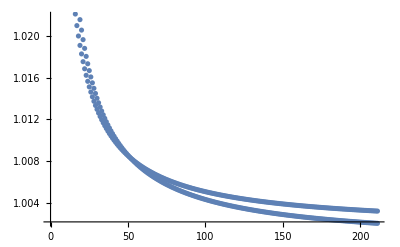

```mathematica
Show[ListPlot[Table[z[n]/asymp[n]//N,{n,3,213}]],ListPlot[Table[z[n]/asymp2[n]//N,{n,3,213}],ColorFunction->"DarkRainbow"]]
```

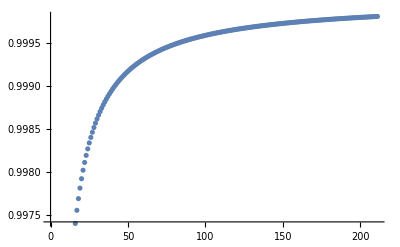

```mathematica
Show[ListPlot[Table[((2n-5)!!)/(√2(2)^(n-2)((n-2)/E)^(n-2))//N,{n,3,213}]]]
```

## Some Test

## Diagrams generation

```mathematica
result=AbsoluteTiming[generatediagrams[6]];
time=result[[1]]
memory=result[[2]]//ByteCount
```

0.11577

1508552

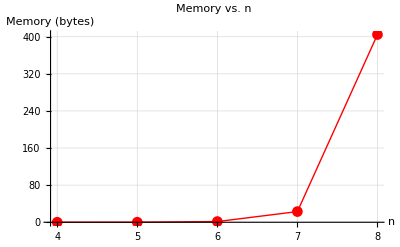

```mathematica
data={{4,0.0011,0.010328},{5,0.0100,0.116064},{6,0.1153,1.508552},{7,1.5998,22.989456},{8,27.5766,404.704280}};

(*Extract the values for n and memory*)
nValues=data[[All,1]];
memoryValues=data[[All,3]];

(*Create the plot*)
ListLinePlot[Transpose[{nValues,memoryValues}],PlotStyle->{Red,Thick},AxesLabel->{"n","Memory (bytes)"},PlotMarkers->Automatic,GridLines->Automatic,PlotRange->All,PlotLabel->"Memory vs. n"]
```

## Amplitude generation

```mathematica
result=generagrafi[4]//Total//AbsoluteTiming;
result[[1]]
(result[[2]]//ByteCount)/1000000//N
```

Total::tllen: Lists of unequal length in {{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1}},{{1,-1},{4,-2},{2,-2},{-1,-2},{3,-1}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}},{{1,-1},{2,-1},{3,-1},{4,-1}}} cannot be added.

0.002379

0.002104

Results for n=7

Expanding

```mathematica
NumberForm[1112.737651,16]
```

1112.737651

```mathematica
NumberForm[4430.251664,16]
```

4430.251664000001

without Expanding

```mathematica
result=(generatediagrams[7]//Total)/.gluon/.V3QCD/.V4QCD/.gprop->propagator/.V3Lorentz->V3p//AbsoluteTiming;
result[[1]]
(result[[2]]//ByteCount)/1000000//N
```

2.48335

51.8192

## Color

```mathematica
{time,f2}=(generatediagrams3[4]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x//AbsoluteTiming
```

{0.003319,{f^c_3c_2a_1 f^c_4c_1a_1,f^c_3c_1a_1 f^c_4c_2a_1,f^c_2c_1a_1 f^c_4c_3a_1}}

```mathematica
{time,f3}=(generatediagrams3[5]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x//Sort//AbsoluteTiming
```

{0.014588,{f^c_3c_2a_2 f^c_4c_1a_1 f^c_5a_2a_1,f^c_3c_1a_1 f^c_4c_2a_2 f^c_5a_2a_1,f^c_2c_1a_1 f^c_4c_3a_2 f^c_5a_2a_1,f^c_3c_2a_2 f^c_4a_2a_1 f^c_5c_1a_1,f^c_3a_2a_1 f^c_4c_2a_2 f^c_5c_1a_1,f^c_2a_2a_1 f^c_4c_3a_2 f^c_5c_1a_1,f^c_1a_2a_1 f^c_4c_3a_2 f^c_5c_2a_1,f^c_3c_1a_1 f^c_4a_2a_1 f^c_5c_2a_2,f^c_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2,f^c_2c_1a_1 f^c_4a_2a_1 f^c_5c_3a_2,f^c_2a_2a_1 f^c_4c_1a_1 f^c_5c_3a_2,f^c_1a_2a_1 f^c_4c_2a_1 f^c_5c_3a_2,f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2,f^c_2a_2a_1 f^c_3c_1a_1 f^c_5c_4a_2,f^c_1a_2a_1 f^c_3c_2a_1 f^c_5c_4a_2}}

```mathematica
{time,f4}=(generatediagrams3[6]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x//Sort//AbsoluteTiming
```

{0.0944,{f^c_3c_2a_2 f^c_4c_1a_1 f^c_5a_3a_2 f^c_6a_3a_1,f^c_3c_1a_1 f^c_4c_2a_2 f^c_5a_3a_2 f^c_6a_3a_1,f^c_2c_1a_1 f^c_4c_3a_2 f^c_5a_3a_2 f^c_6a_3a_1,f^c_3c_2a_2 f^c_4a_3a_2 f^c_5c_1a_1 f^c_6a_3a_1,f^c_3a_3a_2 f^c_4c_2a_2 f^c_5c_1a_1 f^c_6a_3a_1,f^c_2a_3a_2 f^c_4c_3a_2 f^c_5c_1a_1 f^c_6a_3a_1,f^c_1a_3a_2 f^c_4c_3a_2 f^c_5c_2a_1 f^c_6a_3a_1,f^c_3c_1a_1 f^c_4a_3a_2 f^c_5c_2a_2 f^c_6a_3a_1,f^c_3a_3a_2 f^c_4c_1a_1 f^c_5c_2a_2 f^c_6a_3a_1,f^c_2c_1a_1 f^c_4a_3a_2 f^c_5c_3a_2 f^c_6a_3a_1,f^c_2a_3a_2 f^c_4c_1a_1 f^c_5c_3a_2 f^c_6a_3a_1,f^c_1a_3a_2 f^c_4c_2a_1 f^c_5c_3a_2 f^c_6a_3a_1,f^c_2c_1a_1 f^c_3a_3a_2 f^c_5c_4a_2 f^c_6a_3a_1,f^c_2a_3a_2 f^c_3c_1a_1 f^c_5c_4a_2 f^c_6a_3a_1,f^c_1a_3a_2 f^c_3c_2a_1 f^c_5c_4a_2 f^c_6a_3a_1,f^c_3c_2a_2 f^c_4c_1a_1 f^c_5a_3a_1 f^c_6a_3a_2,f^c_3c_1a_1 f^c_4c_2a_2 f^c_5a_3a_1 f^c_6a_3a_2,f^c_2c_1a_1 f^c_4c_3a_2 f^c_5a_3a_1 f^c_6a_3a_2,f^c_3c_2a_2 f^c_4a_3a_1 f^c_5c_1a_1 f^c_6a_3a_2,f^c_3a_3a_1 f^c_4c_2a_2 f^c_5c_1a_1 f^c_6a_3a_2,f^c_2a_3a_1 f^c_4c_3a_2 f^c_5c_1a_1 f^c_6a_3a_2,f^c_1a_3a_1 f^c_4c_3a_2 f^c_5c_2a_1 f^c_6a_3a_2,f^c_3c_1a_1 f^c_4a_3a_1 f^c_5c_2a_2 f^c_6a_3a_2,f^c_3a_3a_1 f^c_4c_1a_1 f^c_5c_2a_2 f^c_6a_3a_2,f^c_2c_1a_1 f^c_4a_3a_1 f^c_5c_3a_2 f^c_6a_3a_2,f^c_2a_3a_1 f^c_4c_1a_1 f^c_5c_3a_2 f^c_6a_3a_2,f^c_1a_3a_1 f^c_4c_2a_1 f^c_5c_3a_2 f^c_6a_3a_2,f^c_2c_1a_1 f^c_3a_3a_1 f^c_5c_4a_2 f^c_6a_3a_2,f^c_2a_3a_1 f^c_3c_1a_1 f^c_5c_4a_2 f^c_6a_3a_2,f^c_1a_3a_1 f^c_3c_2a_1 f^c_5c_4a_2 f^c_6a_3a_2,f^c_3a_3a_2 f^c_4c_2a_2 f^c_5a_3a_1 f^c_6c_1a_1,f^c_2a_3a_2 f^c_4c_3a_2 f^c_5a_3a_1 f^c_6c_1a_1,f^c_3a_3a_1 f^c_4c_2a_2 f^c_5a_3a_2 f^c_6c_1a_1,f^c_2a_3a_1 f^c_4c_3a_2 f^c_5a_3a_2 f^c_6c_1a_1,f^c_3a_3a_2 f^c_4a_3a_1 f^c_5c_2a_2 f^c_6c_1a_1,f^c_3a_3a_1 f^c_4a_3a_2 f^c_5c_2a_2 f^c_6c_1a_1,f^a_3a_2a_1 f^c_4c_3a_3 f^c_5c_2a_2 f^c_6c_1a_1,f^c_2a_3a_2 f^c_4a_3a_1 f^c_5c_3a_2 f^c_6c_1a_1,f^c_2a_3a_1 f^c_4a_3a_2 f^c_5c_3a_2 f^c_6c_1a_1,f^a_3a_2a_1 f^c_4c_2a_2 f^c_5c_3a_3 f^c_6c_1a_1,f^c_2a_3a_2 f^c_3a_3a_1 f^c_5c_4a_2 f^c_6c_1a_1,f^c_2a_3a_1 f^c_3a_3a_2 f^c_5c_4a_2 f^c_6c_1a_1,f^c_3c_2a_1 f^c_4a_3a_2 f^c_5a_3a_1 f^c_6c_1a_2,f^c_3c_2a_1 f^c_4a_3a_1 f^c_5a_3a_2 f^c_6c_1a_2,f^a_3a_2a_1 f^c_3c_2a_1 f^c_5c_4a_3 f^c_6c_1a_2,f^c_1a_3a_2 f^c_4a_3a_1 f^c_5c_3a_2 f^c_6c_2a_1,f^c_1a_3a_1 f^c_4a_3a_2 f^c_5c_3a_2 f^c_6c_2a_1,f^c_1a_3a_2 f^c_3a_3a_1 f^c_5c_4a_2 f^c_6c_2a_1,f^c_1a_3a_1 f^c_3a_3a_2 f^c_5c_4a_2 f^c_6c_2a_1,f^c_3c_1a_1 f^c_4a_3a_2 f^c_5a_3a_1 f^c_6c_2a_2,f^c_3a_3a_2 f^c_4c_1a_1 f^c_5a_3a_1 f^c_6c_2a_2,f^c_1a_3a_2 f^c_4c_3a_1 f^c_5a_3a_1 f^c_6c_2a_2,f^c_3c_1a_1 f^c_4a_3a_1 f^c_5a_3a_2 f^c_6c_2a_2,f^c_3a_3a_1 f^c_4c_1a_1 f^c_5a_3a_2 f^c_6c_2a_2,f^c_1a_3a_1 f^c_4c_3a_1 f^c_5a_3a_2 f^c_6c_2a_2,f^c_3a_3a_2 f^c_4a_3a_1 f^c_5c_1a_1 f^c_6c_2a_2,f^c_3a_3a_1 f^c_4a_3a_2 f^c_5c_1a_1 f^c_6c_2a_2,f^a_3a_2a_1 f^c_4c_1a_1 f^c_5c_3a_3 f^c_6c_2a_2,f^a_3a_2a_1 f^c_3c_1a_1 f^c_5c_4a_3 f^c_6c_2a_2,f^a_3a_2a_1 f^c_4c_3a_2 f^c_5c_1a_1 f^c_6c_2a_3,f^c_1a_3a_2 f^c_2a_3a_1 f^c_5c_4a_2 f^c_6c_3a_1,f^c_1a_3a_1 f^c_2a_3a_2 f^c_5c_4a_2 f^c_6c_3a_1,f^c_2c_1a_1 f^c_4a_3a_2 f^c_5a_3a_1 f^c_6c_3a_2,f^c_2a_3a_2 f^c_4c_1a_1 f^c_5a_3a_1 f^c_6c_3a_2,f^c_1a_3a_2 f^c_4c_2a_1 f^c_5a_3a_1 f^c_6c_3a_2,f^c_2c_1a_1 f^c_4a_3a_1 f^c_5a_3a_2 f^c_6c_3a_2,f^c_2a_3a_1 f^c_4c_1a_1 f^c_5a_3a_2 f^c_6c_3a_2,f^c_1a_3a_1 f^c_4c_2a_1 f^c_5a_3a_2 f^c_6c_3a_2,f^c_2a_3a_2 f^c_4a_3a_1 f^c_5c_1a_1 f^c_6c_3a_2,f^c_2a_3a_1 f^c_4a_3a_2 f^c_5c_1a_1 f^c_6c_3a_2,f^c_1a_3a_2 f^c_4a_3a_1 f^c_5c_2a_1 f^c_6c_3a_2,f^c_1a_3a_1 f^c_4a_3a_2 f^c_5c_2a_1 f^c_6c_3a_2,f^a_3a_2a_1 f^c_2c_1a_1 f^c_5c_4a_3 f^c_6c_3a_2,f^a_3a_2a_1 f^c_4c_2a_2 f^c_5c_1a_1 f^c_6c_3a_3,f^a_3a_2a_1 f^c_4c_1a_1 f^c_5c_2a_2 f^c_6c_3a_3,f^c_2c_1a_1 f^c_3a_3a_2 f^c_5a_3a_1 f^c_6c_4a_2,f^c_2a_3a_2 f^c_3c_1a_1 f^c_5a_3a_1 f^c_6c_4a_2,f^c_1a_3a_2 f^c_3c_2a_1 f^c_5a_3a_1 f^c_6c_4a_2,f^c_2c_1a_1 f^c_3a_3a_1 f^c_5a_3a_2 f^c_6c_4a_2,f^c_2a_3a_1 f^c_3c_1a_1 f^c_5a_3a_2 f^c_6c_4a_2,f^c_1a_3a_1 f^c_3c_2a_1 f^c_5a_3a_2 f^c_6c_4a_2,f^c_2a_3a_2 f^c_3a_3a_1 f^c_5c_1a_1 f^c_6c_4a_2,f^c_2a_3a_1 f^c_3a_3a_2 f^c_5c_1a_1 f^c_6c_4a_2,f^c_1a_3a_2 f^c_3a_3a_1 f^c_5c_2a_1 f^c_6c_4a_2,f^c_1a_3a_1 f^c_3a_3a_2 f^c_5c_2a_1 f^c_6c_4a_2,f^c_1a_3a_2 f^c_2a_3a_1 f^c_5c_3a_1 f^c_6c_4a_2,f^c_1a_3a_1 f^c_2a_3a_2 f^c_5c_3a_1 f^c_6c_4a_2,f^a_3a_2a_1 f^c_3c_2a_2 f^c_5c_1a_1 f^c_6c_4a_3,f^a_3a_2a_1 f^c_3c_1a_1 f^c_5c_2a_2 f^c_6c_4a_3,f^a_3a_2a_1 f^c_2c_1a_1 f^c_5c_3a_2 f^c_6c_4a_3,f^c_2c_1a_1 f^c_3a_3a_2 f^c_4a_3a_1 f^c_6c_5a_2,f^c_2a_3a_2 f^c_3c_1a_1 f^c_4a_3a_1 f^c_6c_5a_2,f^c_1a_3a_2 f^c_3c_2a_1 f^c_4a_3a_1 f^c_6c_5a_2,f^c_2c_1a_1 f^c_3a_3a_1 f^c_4a_3a_2 f^c_6c_5a_2,f^c_2a_3a_1 f^c_3c_1a_1 f^c_4a_3a_2 f^c_6c_5a_2,f^c_1a_3a_1 f^c_3c_2a_1 f^c_4a_3a_2 f^c_6c_5a_2,f^c_2a_3a_2 f^c_3a_3a_1 f^c_4c_1a_1 f^c_6c_5a_2,f^c_2a_3a_1 f^c_3a_3a_2 f^c_4c_1a_1 f^c_6c_5a_2,f^c_1a_3a_2 f^c_3a_3a_1 f^c_4c_2a_1 f^c_6c_5a_2,f^c_1a_3a_1 f^c_3a_3a_2 f^c_4c_2a_1 f^c_6c_5a_2,f^c_1a_3a_2 f^c_2a_3a_1 f^c_4c_3a_1 f^c_6c_5a_2,f^c_1a_3a_1 f^c_2a_3a_2 f^c_4c_3a_1 f^c_6c_5a_2,f^a_3a_2a_1 f^c_3c_2a_2 f^c_4c_1a_1 f^c_6c_5a_3,f^a_3a_2a_1 f^c_3c_1a_1 f^c_4c_2a_2 f^c_6c_5a_3,f^a_3a_2a_1 f^c_2c_1a_1 f^c_4c_3a_2 f^c_6c_5a_3}}

```mathematica
{time,f5}=(generatediagrams3[7]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x//Sort//AbsoluteTiming
```

```mathematica
{time,f6}=(generatediagrams3[8]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x//Sort//AbsoluteTiming
```

```mathematica
(f2[[1]]/.a->b)f2[[1]]//Color//AbsoluteTiming
```

{0.033042,Nc^2 (-1+Nc^2)}

```mathematica
(f2[[1]]/.a->b)f2[[2]]
```

f^c_3c_1a_1 f^c_3c_2b_1 f^c_4c_1b_1 f^c_4c_2a_1

```mathematica
(f2[[1]]/.a->b)f2[[2]]//Color//AbsoluteTiming
```

{0.035638,1/2 Nc^2 (-1+Nc^2)}

```mathematica
(f3[[1]]/.a->b)f3[[2]]
```

f^c_1b_2b_1 f^c_3c_2a_2 f^c_3c_2b_1 f^c_4a_2a_1 f^c_5c_1a_1 f^c_5c_4b_2

```mathematica
(f3[[1]]/.a->b)f3[[2]]//Color//AbsoluteTiming
```

{0.070698,-1/2 Nc^3 (-1+Nc^2)}

```mathematica
(f3[[1]]/.a->b)f3[[1]]//Color//AbsoluteTiming
```

{0.077311,-Nc^3+Nc^5}

```mathematica
(f4[[1]]/.a->b)f4[[2]]
```

f^c_1a_3a_1 f^c_1b_3b_1 f^c_3c_2a_1 f^c_3c_2b_1 f^c_4b_3b_2 f^c_5a_3a_2 f^c_6c_4a_2 f^c_6c_5b_2

```mathematica
(f4[[1]]/.a->b)f4[[2]]//Color//AbsoluteTiming
```

{0.287873,1/2 Nc^4 (-1+Nc^2)}

```mathematica
(f4[[1]]/.a->b)f4[[1]]//Color//AbsoluteTiming
```

{0.298724,Nc^4 (-1+Nc^2)}

```mathematica
products=(generatediagrams3[4]/.V3ColorOnly/.propColorOnly//Expand//ColorDelta//frule)/.-x_:>x
```

{f^c_3c_2a_1 f^c_4c_1a_1,f^c_3c_1a_1 f^c_4c_2a_1,f^c_2c_1a_1 f^c_4c_3a_1}

```mathematica
rule=#/.MapIndexed[#1->v[First[#2]]&,f2]&;
```

```mathematica
List@@Collect[generatediagrams[4]//Total//FeynmanRules//frule//Contract//Simplify,_f][[All,2;;3]]//Jacobi//rule
```

{v_2-v_3,v_2,v_3}

## Generating color substructure from specific Feynman diagrams instead of isolating them from all the the Feynman Diagrams

### n = 4

```mathematica
grafi4=generagrafi[4];
```

```mathematica
result=Select[grafi4,MemberQ[#,{4,-2}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi4,#]&/@result
```

{{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}}

{{{3}}}

```mathematica
result=Select[grafi4,MemberQ[#,{4,-1}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi4,#]&/@result
```

{{{1,-1},{2,-1},{3,-1},{4,-1}}}

{{{4}}}

### n = 5

```mathematica
grafi5=generagrafi[5];
```

```mathematica
ver3=Select[grafi5,MemberQ[#,{5,-3}] &&MemberQ[#,{4,-3}]&&MemberQ[#,{2,-1}]&&MemberQ[#,{1,-1}]&]
Position[grafi5,#]&/@ ver3
```

{{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2}}}

{{{13}}}

```mathematica
(grafi5[[13]]//Diagrams//FeynmanRules//frule//Simplify)[[1;;3]]
```

f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2

```mathematica
ver4=Select[grafi5,MemberQ[#,{5,-2}]&&MemberQ[#,{4,-2}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi5,#]&/@ ver4
```

{{{1,-1},{2,-1},{3,-1},{5,-2},{4,-2},{-1,-2}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{5,-2}}}

{{{19}},{{25}}}

```mathematica
(grafi5[[19]]//Diagrams//FeynmanRules//frule//Simplify)[[1;;3]]
```

f^c_5c_4a_2 (f^c_2c_1a_1 f^c_3a_2a_1 (η_(μ_1μ_(-2,-1)) η_μ_2μ_3-η_μ_1μ_3 η_(μ_2μ_(-2,-1)))+f^c_2a_2a_1 f^c_3c_1a_1 (η_(μ_1μ_(-2,-1)) η_μ_2μ_3-η_μ_1μ_2 η_(μ_3μ_(-2,-1)))+f^c_1a_2a_1 f^c_3c_2a_1 (η_μ_1μ_3 η_(μ_2μ_(-2,-1))-η_μ_1μ_2 η_(μ_3μ_(-2,-1)))) η_(μ_(-2,-1)μ_(-1,-2))

### n = 6

```mathematica
grafi6=generagrafi[6];
```

```mathematica
ver3=Select[grafi6,MemberQ[#,{6,-4}] &&MemberQ[#,{5,-4}]&&MemberQ[#,{2,-1}]&&MemberQ[#,{1,-1}]&]
Position[grafi6,#]&/@ ver3
```

{{{1,-1},{2,-1},{6,-4},{5,-4},{-3,-4},{4,-3},{-2,-3},{3,-2},{-1,-2}},{{1,-1},{2,-1},{4,-2},{6,-4},{5,-4},{-3,-4},{3,-3},{-2,-3},{-1,-2}},{{1,-1},{2,-1},{4,-2},{3,-2},{6,-4},{5,-4},{-3,-4},{-1,-3},{-2,-3}}}

{{{87}},{{95}},{{103}}}

```mathematica
(grafi6[[87]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;5]]
```

f^c_2c_1a_1 f^c_3a_3a_1 f^c_4a_3a_2 f^c_6c_5a_2

```mathematica
ver4=Select[grafi6,MemberQ[#,{6,-3}]&&MemberQ[#,{5,-3}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi6,#]&/@ ver4
```

{{{1,-1},{2,-1},{6,-3},{5,-3},{-2,-3},{3,-2},{-1,-2},{4,-1}},{{1,-1},{2,-1},{3,-1},{6,-3},{5,-3},{-2,-3},{4,-2},{-1,-2}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-1,-3}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-2,-3}},{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2},{6,-3}},{{1,-1},{2,-1},{4,-2},{5,-3},{3,-3},{-2,-3},{-1,-2},{6,-3}},{{1,-1},{2,-1},{4,-2},{3,-2},{5,-3},{-1,-3},{-2,-3},{6,-3}}}

{{{120}},{{127}},{{159}},{{165}},{{204}},{{207}},{{210}}}

```mathematica
grafi6[[210]]
(grafi6[[210]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{5,-3},{-1,-3},{-2,-3},{6,-3}}

f^c_2c_1a_1 f^c_4c_3a_2 η_(μ_(-3,-2)μ_(-2,-3))

```mathematica
grafi6[[207]]
(grafi6[[207]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{4,-2},{5,-3},{3,-3},{-2,-3},{-1,-2},{6,-3}}

f^c_2c_1a_1 f^c_4a_3a_1 (f^c_5c_3a_2 f^c_6a_3a_2 (η_(μ_3μ_(-2,-3)) η_μ_5μ_6-η_μ_3μ_6 η_(μ_5μ_(-2,-3)))+f^c_5a_3a_2 f^c_6c_3a_2 (η_(μ_3μ_(-2,-3)) η_μ_5μ_6-η_μ_3μ_5 η_(μ_6μ_(-2,-3)))+f^c_3a_3a_2 f^c_6c_5a_2 (η_μ_3μ_6 η_(μ_5μ_(-2,-3))-η_μ_3μ_5 η_(μ_6μ_(-2,-3))))

```mathematica
grafi6[[165]]
(grafi6[[165]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-2,-3}}

f^c_2c_1a_1 η_(μ_(-3,-2)μ_(-2,-3)) (f^a_3a_2a_1 f^c_4c_3a_2 f^c_6c_5a_3 (η_(μ_3μ_(-1,-2)) η_(μ_4μ_(-3,-2))-η_(μ_3μ_(-3,-2)) η_(μ_4μ_(-1,-2)))+f^c_3a_3a_2 f^c_4a_3a_1 f^c_6c_5a_2 (η_(μ_3μ_(-1,-2)) η_(μ_4μ_(-3,-2))-η_μ_3μ_4 η_(μ_(-3,-2)μ_(-1,-2)))+f^c_3a_3a_1 f^c_4a_3a_2 f^c_6c_5a_2 (η_(μ_3μ_(-3,-2)) η_(μ_4μ_(-1,-2))-η_μ_3μ_4 η_(μ_(-3,-2)μ_(-1,-2))))

```mathematica
grafi6[[204]]
(grafi6[[204]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2},{6,-3}}

f^c_2c_1a_1 f^c_3a_3a_1 (f^c_5c_4a_2 f^c_6a_3a_2 (η_(μ_4μ_(-2,-3)) η_μ_5μ_6-η_μ_4μ_6 η_(μ_5μ_(-2,-3)))+f^c_5a_3a_2 f^c_6c_4a_2 (η_(μ_4μ_(-2,-3)) η_μ_5μ_6-η_μ_4μ_5 η_(μ_6μ_(-2,-3)))+f^c_4a_3a_2 f^c_6c_5a_2 (η_μ_4μ_6 η_(μ_5μ_(-2,-3))-η_μ_4μ_5 η_(μ_6μ_(-2,-3))))

```mathematica
ver4=Select[grafi6,MemberQ[#,{6,-2}]&&MemberQ[#,{5,-2}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi6,#]&/@ ver4
```

{{{1,-1},{2,-1},{5,-2},{3,-2},{-1,-2},{4,-1},{6,-2}},{{1,-1},{2,-1},{3,-1},{5,-2},{4,-2},{-1,-2},{6,-2}}}

{{{213}},{{214}}}

```mathematica
grafi6[[214]]
(grafi6[[214]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{3,-1},{5,-2},{4,-2},{-1,-2},{6,-2}}

(f^c_2c_1a_1 f^c_3a_3a_1 (η_(μ_1μ_(-2,-1)) η_μ_2μ_3-η_μ_1μ_3 η_(μ_2μ_(-2,-1)))+f^c_2a_3a_1 f^c_3c_1a_1 (η_(μ_1μ_(-2,-1)) η_μ_2μ_3-η_μ_1μ_2 η_(μ_3μ_(-2,-1)))+f^c_1a_3a_1 f^c_3c_2a_1 (η_μ_1μ_3 η_(μ_2μ_(-2,-1))-η_μ_1μ_2 η_(μ_3μ_(-2,-1)))) (f^c_5c_4a_2 f^c_6a_3a_2 (η_(μ_4μ_(-1,-2)) η_μ_5μ_6-η_μ_4μ_6 η_(μ_5μ_(-1,-2)))+f^c_5a_3a_2 f^c_6c_4a_2 (η_(μ_4μ_(-1,-2)) η_μ_5μ_6-η_μ_4μ_5 η_(μ_6μ_(-1,-2)))+f^c_4a_3a_2 f^c_6c_5a_2 (η_μ_4μ_6 η_(μ_5μ_(-1,-2))-η_μ_4μ_5 η_(μ_6μ_(-1,-2)))) η_(μ_(-2,-1)μ_(-1,-2))

```mathematica
masterInsert[grafo_]:=Module[{nuovigrafi,indici,npt,nvert},
indici = Flatten[grafo]; (*Convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
pos=Position[grafo,{npt,nvert}]//Max;
If[Count[grafo,nvert,2]===3,
nuovigrafi=List[inserisci3[pos,npt+1,nvert-1,grafo],inserisci4[nvert,npt+1,grafo]],
nuovigrafi=List[inserisci3[pos,npt+1,nvert-1,grafo]]
];
Return[nuovigrafi]
]
(*generate only graphs which contribute to f[c1,c2,a1]f[c3,a2,a1]f[c4,a3,a2]f[c5,a4,a3]...f[c_n,c_n-1,a_n-3]*)
generatemastergraph[n_]:=Module[{mastergraphs,i},
i=3;
mastergraphs = {grafobase};
While[i<n,
mastergraphs = Map[masterInsert,mastergraphs]; (*vectorized*)
mastergraphs = Flatten[mastergraphs,1];
++i;
];
Return[mastergraphs]
]
```

```mathematica
generatemastergraph[4][[1]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}

```mathematica
grafi4[[3]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}

```mathematica
generatemastergraph[5][[1]]
```

{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2}}

```mathematica
grafi5[[13]]
```

{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2}}

```mathematica
generatemastergraph[6][[1]]
```

{{1,-1},{2,-1},{6,-4},{5,-4},{-3,-4},{4,-3},{-2,-3},{3,-2},{-1,-2}}

```mathematica
grafi6[[87]]
```

{{1,-1},{2,-1},{6,-4},{5,-4},{-3,-4},{4,-3},{-2,-3},{3,-2},{-1,-2}}

```mathematica
generatemastergraph[6]-List[grafi6[[87]],grafi6[[204]],grafi6[[165]],grafi6[[127]],grafi6[[214]]]
```

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

```mathematica
grafo=grafi5[[25]]; 
indici = Flatten[grafo]; (*Convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
pos=Position[grafo,{npt,nvert}]//Max;
If[Count[grafo,nvert,2]===3,
nuovografo=List[inserisci3[pos,npt+1,nvert-1,grafo],inserisci4[nvert,npt+1,grafo]],
nuovografo=List[inserisci3[pos,npt+1,nvert-1,grafo]]
]
```

{{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-2,-3}}}

```mathematica
grafi6[[165]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-2,-3}}

```mathematica
generatemasterdiagrams[4][[1]]/.V3ColorOnly/.propColorOnly//ColorDelta//frule
```

-f^c_2c_1a_1 f^c_4c_3a_1

```mathematica
rule3=#/.MapIndexed[#1->v[First[#2]]&,f3]&;
```

```mathematica
master5=Collect[generatemasterdiagrams[5]//FeynmanRules//frule//rule3//Total,_v]/.v[i_/; i=!=13]:>0/.v[13]:>1//AbsoluteTiming;
```

```mathematica
real5=Collect[generatediagrams[5]//FeynmanRules//frule//rule3//Total,_v]/.v[i_/; i=!=13]:>0/.v[13]:>1//AbsoluteTiming;
```

```mathematica
real5-master5
```

{0.163909,0}

```mathematica
rule4=#/.MapIndexed[#1->v[First[#2]]&,f4]&;
```

```mathematica
master6=Collect[generatemasterdiagrams[6]//FeynmanRules//frule//rule4//Total,_v]/.v[i_/; i=!=87]:>0/.v[87]:>1//AbsoluteTiming;
```

```mathematica
real6=Collect[generatediagrams[6]//FeynmanRules//frule//rule4//Total,_v]/.v[i_/; i=!=87]:>0/.v[87]:>1//AbsoluteTiming;
```

```mathematica
master6[[1]]
```

0.159278

```mathematica
real6[[1]]
```

11.6481

```mathematica
real6-master6
```

{11.4888,0}

## Generating Color Ordered Amplitude from specific Feynman diagrams instead of isolating them from all the the Feynman Diagrams

### n = 4

```mathematica
grafi4=generagrafi[4];
```

```mathematica
s=Select[grafi4,MemberQ[#,{4,-2}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi4,#]&/@s
```

{{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}}

{{{3}}}

```mathematica
grafi4[[3]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}

```mathematica
ContainsAll[grafi4[[3]],{{-1,-2},{4,-2},{3,-2}}]
```

True

```mathematica
u=Select[grafi4,MemberQ[#,{4,-2}]&&MemberQ[#,{1,-2}]&&MemberQ[#,{2,-1}]&]
Position[grafi4,#]&/@u
```

{{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1}}}

{{{1}}}

```mathematica
v4=Select[grafi4,MemberQ[#,{4,-1}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi4,#]&/@v4
```

{{{1,-1},{2,-1},{3,-1},{4,-1}}}

{{{4}}}

### n = 5

```mathematica
grafi5=generagrafi[5];
```

```mathematica
s=Select[grafi5,MemberQ[#,{5,-3}] &&MemberQ[#,{4,-3}]&&MemberQ[#,{2,-1}]&&MemberQ[#,{1,-1}]&]
Position[grafi5,#]&/@ s
```

{{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2}}}

{{{13}}}

```mathematica
s=Select[grafi5,MemberQ[#,{5,-3}] &&MemberQ[#,{4,-3}]&&MemberQ[#,{2,-1}]&&MemberQ[#,{1,-1}]&]
Position[grafi5,#]&/@ s
```

```mathematica
(grafi5[[13]]//Diagrams//FeynmanRules//frule//Simplify)[[1;;3]]
```

f^c_2c_1a_1 f^c_3a_2a_1 f^c_5c_4a_2

```mathematica
ver4=Select[grafi5,MemberQ[#,{5,-2}]&&MemberQ[#,{4,-2}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi5,#]&/@ ver4
```

{{{1,-1},{2,-1},{3,-1},{5,-2},{4,-2},{-1,-2}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{5,-2}}}

{{{19}},{{25}}}

```mathematica
(grafi5[[19]]//Diagrams//FeynmanRules//frule//Simplify)[[1;;3]]
```

f^c_5c_4a_2 (f^c_2c_1a_1 f^c_3a_2a_1 (η_(μ_1μ_(-2,-1)) η_μ_2μ_3-η_μ_1μ_3 η_(μ_2μ_(-2,-1)))+f^c_2a_2a_1 f^c_3c_1a_1 (η_(μ_1μ_(-2,-1)) η_μ_2μ_3-η_μ_1μ_2 η_(μ_3μ_(-2,-1)))+f^c_1a_2a_1 f^c_3c_2a_1 (η_μ_1μ_3 η_(μ_2μ_(-2,-1))-η_μ_1μ_2 η_(μ_3μ_(-2,-1)))) η_(μ_(-2,-1)μ_(-1,-2))

### n = 6

```mathematica
grafi6=generagrafi[6];
```

```mathematica
ver3=Select[grafi6,MemberQ[#,{6,-4}] &&MemberQ[#,{5,-4}]&&MemberQ[#,{2,-1}]&&MemberQ[#,{1,-1}]&]
Position[grafi6,#]&/@ ver3
```

{{{1,-1},{2,-1},{6,-4},{5,-4},{-3,-4},{4,-3},{-2,-3},{3,-2},{-1,-2}},{{1,-1},{2,-1},{4,-2},{6,-4},{5,-4},{-3,-4},{3,-3},{-2,-3},{-1,-2}},{{1,-1},{2,-1},{4,-2},{3,-2},{6,-4},{5,-4},{-3,-4},{-1,-3},{-2,-3}}}

{{{87}},{{95}},{{103}}}

```mathematica
(grafi6[[87]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;5]]
```

f^c_2c_1a_1 f^c_3a_3a_1 f^c_4a_3a_2 f^c_6c_5a_2

```mathematica
ver4=Select[grafi6,MemberQ[#,{6,-3}]&&MemberQ[#,{5,-3}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi6,#]&/@ ver4
```

{{{1,-1},{2,-1},{6,-3},{5,-3},{-2,-3},{3,-2},{-1,-2},{4,-1}},{{1,-1},{2,-1},{3,-1},{6,-3},{5,-3},{-2,-3},{4,-2},{-1,-2}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-1,-3}},{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-2,-3}},{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2},{6,-3}},{{1,-1},{2,-1},{4,-2},{5,-3},{3,-3},{-2,-3},{-1,-2},{6,-3}},{{1,-1},{2,-1},{4,-2},{3,-2},{5,-3},{-1,-3},{-2,-3},{6,-3}}}

{{{120}},{{127}},{{159}},{{165}},{{204}},{{207}},{{210}}}

```mathematica
grafi6[[210]]
(grafi6[[210]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{5,-3},{-1,-3},{-2,-3},{6,-3}}

f^c_2c_1a_1 f^c_4c_3a_2 η_(μ_(-3,-2)μ_(-2,-3))

```mathematica
grafi6[[207]]
(grafi6[[207]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{4,-2},{5,-3},{3,-3},{-2,-3},{-1,-2},{6,-3}}

f^c_2c_1a_1 f^c_4a_3a_1 (f^c_5c_3a_2 f^c_6a_3a_2 (η_(μ_3μ_(-2,-3)) η_μ_5μ_6-η_μ_3μ_6 η_(μ_5μ_(-2,-3)))+f^c_5a_3a_2 f^c_6c_3a_2 (η_(μ_3μ_(-2,-3)) η_μ_5μ_6-η_μ_3μ_5 η_(μ_6μ_(-2,-3)))+f^c_3a_3a_2 f^c_6c_5a_2 (η_μ_3μ_6 η_(μ_5μ_(-2,-3))-η_μ_3μ_5 η_(μ_6μ_(-2,-3))))

```mathematica
grafi6[[165]]
(grafi6[[165]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-2,-3}}

f^c_2c_1a_1 η_(μ_(-3,-2)μ_(-2,-3)) (f^a_3a_2a_1 f^c_4c_3a_2 f^c_6c_5a_3 (η_(μ_3μ_(-1,-2)) η_(μ_4μ_(-3,-2))-η_(μ_3μ_(-3,-2)) η_(μ_4μ_(-1,-2)))+f^c_3a_3a_2 f^c_4a_3a_1 f^c_6c_5a_2 (η_(μ_3μ_(-1,-2)) η_(μ_4μ_(-3,-2))-η_μ_3μ_4 η_(μ_(-3,-2)μ_(-1,-2)))+f^c_3a_3a_1 f^c_4a_3a_2 f^c_6c_5a_2 (η_(μ_3μ_(-3,-2)) η_(μ_4μ_(-1,-2))-η_μ_3μ_4 η_(μ_(-3,-2)μ_(-1,-2))))

```mathematica
grafi6[[204]]
(grafi6[[204]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2},{6,-3}}

f^c_2c_1a_1 f^c_3a_3a_1 (f^c_5c_4a_2 f^c_6a_3a_2 (η_(μ_4μ_(-2,-3)) η_μ_5μ_6-η_μ_4μ_6 η_(μ_5μ_(-2,-3)))+f^c_5a_3a_2 f^c_6c_4a_2 (η_(μ_4μ_(-2,-3)) η_μ_5μ_6-η_μ_4μ_5 η_(μ_6μ_(-2,-3)))+f^c_4a_3a_2 f^c_6c_5a_2 (η_μ_4μ_6 η_(μ_5μ_(-2,-3))-η_μ_4μ_5 η_(μ_6μ_(-2,-3))))

```mathematica
ver4=Select[grafi6,MemberQ[#,{6,-2}]&&MemberQ[#,{5,-2}]&&MemberQ[#,{1,-1}]&&MemberQ[#,{2,-1}]&]
Position[grafi6,#]&/@ ver4
```

{{{1,-1},{2,-1},{5,-2},{3,-2},{-1,-2},{4,-1},{6,-2}},{{1,-1},{2,-1},{3,-1},{5,-2},{4,-2},{-1,-2},{6,-2}}}

{{{213}},{{214}}}

```mathematica
grafi6[[214]]
(grafi6[[214]]//Diagrams//FeynmanRules//frule//Simplify)[[2;;4]]
```

{{1,-1},{2,-1},{3,-1},{5,-2},{4,-2},{-1,-2},{6,-2}}

(f^c_2c_1a_1 f^c_3a_3a_1 (η_(μ_1μ_(-2,-1)) η_μ_2μ_3-η_μ_1μ_3 η_(μ_2μ_(-2,-1)))+f^c_2a_3a_1 f^c_3c_1a_1 (η_(μ_1μ_(-2,-1)) η_μ_2μ_3-η_μ_1μ_2 η_(μ_3μ_(-2,-1)))+f^c_1a_3a_1 f^c_3c_2a_1 (η_μ_1μ_3 η_(μ_2μ_(-2,-1))-η_μ_1μ_2 η_(μ_3μ_(-2,-1)))) (f^c_5c_4a_2 f^c_6a_3a_2 (η_(μ_4μ_(-1,-2)) η_μ_5μ_6-η_μ_4μ_6 η_(μ_5μ_(-1,-2)))+f^c_5a_3a_2 f^c_6c_4a_2 (η_(μ_4μ_(-1,-2)) η_μ_5μ_6-η_μ_4μ_5 η_(μ_6μ_(-1,-2)))+f^c_4a_3a_2 f^c_6c_5a_2 (η_μ_4μ_6 η_(μ_5μ_(-1,-2))-η_μ_4μ_5 η_(μ_6μ_(-1,-2)))) η_(μ_(-2,-1)μ_(-1,-2))

```mathematica
masterInsert[grafo_]:=Module[{nuovigrafi,indici,npt,nvert},
indici = Flatten[grafo]; (*Convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
pos=Position[grafo,{npt,nvert}]//Max;
If[Count[grafo,nvert,2]===3,
nuovigrafi=List[inserisci3[pos,npt+1,nvert-1,grafo],inserisci4[nvert,npt+1,grafo]],
nuovigrafi=List[inserisci3[pos,npt+1,nvert-1,grafo]]
];
Return[nuovigrafi]
]
(*generate only graphs which contribute to f[c1,c2,a1]f[c3,a2,a1]f[c4,a3,a2]f[c5,a4,a3]...f[c_n,c_n-1,a_n-3]*)
generatemastergraph[n_]:=Module[{mastergraphs,i},
i=3;
mastergraphs = {grafobase};
While[i<n,
mastergraphs = Map[masterInsert,mastergraphs]; (*vectorized*)
mastergraphs = Flatten[mastergraphs,1];
++i;
];
Return[mastergraphs]
]
```

```mathematica
generatemastergraph[4][[1]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}

```mathematica
grafi4[[3]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}

```mathematica
generatemastergraph[5][[1]]
```

{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2}}

```mathematica
grafi5[[13]]
```

{{1,-1},{2,-1},{5,-3},{4,-3},{-2,-3},{3,-2},{-1,-2}}

```mathematica
generatemastergraph[6][[1]]
```

{{1,-1},{2,-1},{6,-4},{5,-4},{-3,-4},{4,-3},{-2,-3},{3,-2},{-1,-2}}

```mathematica
grafi6[[87]]
```

{{1,-1},{2,-1},{6,-4},{5,-4},{-3,-4},{4,-3},{-2,-3},{3,-2},{-1,-2}}

```mathematica
generatemastergraph[6]-List[grafi6[[87]],grafi6[[204]],grafi6[[165]],grafi6[[127]],grafi6[[214]]]
```

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

```mathematica
grafo=grafi5[[25]]; 
indici = Flatten[grafo]; (*Convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
pos=Position[grafo,{npt,nvert}]//Max;
If[Count[grafo,nvert,2]===3,
nuovografo=List[inserisci3[pos,npt+1,nvert-1,grafo],inserisci4[nvert,npt+1,grafo]],
nuovografo=List[inserisci3[pos,npt+1,nvert-1,grafo]]
]
```

{{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-2,-3}}}

```mathematica
grafi6[[165]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{6,-3},{5,-3},{-2,-3}}

```mathematica
generatemasterdiagrams[4][[1]]/.V3ColorOnly/.propColorOnly//ColorDelta//frule
```

-f^c_2c_1a_1 f^c_4c_3a_1

```mathematica
rule3=#/.MapIndexed[#1->v[First[#2]]&,f3]&;
```

```mathematica
master5=Collect[generatemasterdiagrams[5]//FeynmanRules//frule//rule3//Total,_v]/.v[i_/; i=!=13]:>0/.v[13]:>1//AbsoluteTiming;
```

```mathematica
real5=Collect[generatediagrams[5]//FeynmanRules//frule//rule3//Total,_v]/.v[i_/; i=!=13]:>0/.v[13]:>1//AbsoluteTiming;
```

```mathematica
real5-master5
```

{0.163909,0}

```mathematica
rule4=#/.MapIndexed[#1->v[First[#2]]&,f4]&;
```

```mathematica
master6=Collect[generatemasterdiagrams[6]//FeynmanRules//frule//rule4//Total,_v]/.v[i_/; i=!=87]:>0/.v[87]:>1//AbsoluteTiming;
```

```mathematica
real6=Collect[generatediagrams[6]//FeynmanRules//frule//rule4//Total,_v]/.v[i_/; i=!=87]:>0/.v[87]:>1//AbsoluteTiming;
```

```mathematica
master6[[1]]
```

0.159278

```mathematica
real6[[1]]
```

11.6481

```mathematica
real6-master6
```

{11.4888,0}

```mathematica
grafi4[[3]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2}}

```mathematica
grafo=grafi4[[1]]
indici = Flatten[grafo]; (*Convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
pos=Position[grafo,{npt,_}]//Max;
vert=grafo[[pos]][[2]];
pos2=Position[grafo,{1,_}]//Max;
vert2=grafo[[pos2]][[2]];
If[Count[grafo,nvert,2]===3,
nuovigrafi=List[inserisci3[pos,npt+1,vert-1,grafo],inserisci4[vert,npt+1,grafo],inserisci3[pos2,npt+1,vert-1,grafo],inserisci4[vert2,npt+1,grafo]],
nuovigrafi=List[inserisci3[pos,npt+1,nvert-1,grafo],inserisci3[pos2,npt+1,nvert-1,grafo]]//DeleteDuplicates
];
If[ContainsAll[grafo,{{npt,nvert},{npt-1,nvert},{nvert+1,nvert}}] && Count[grafo,nvert,2]===3,
pos=Position[grafo,{nvert+1,nvert}]//Max;
AppendTo[nuovigrafi,inserisci3[pos,npt+1,nvert-1,grafo]]
];
DeleteCases[nuovigrafi//DeleteDuplicates,{}]
```

{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1}}

{{{5,-3},{4,-3},{-2,-3},{1,-2},{-1,-2},{2,-1},{3,-1}},{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1},{5,-2}},{{4,-2},{5,-3},{1,-3},{-2,-3},{-1,-2},{2,-1},{3,-1}}}

{{4,-2},{5,-3},{1,-3},{-2,-3},{-1,-2},{2,-1},{3,-1}}

```mathematica
grafi5[[16]]
```

{{5,-2},{1,-2},{-1,-2},{2,-1},{3,-1},{4,-1}}

```mathematica
generateMastergraph[8]//Length
```

60

```mathematica
generateMastergraph[6][[3]]
```

{{1,-1},{2,-1},{5,-3},{4,-3},{6,-4},{-2,-4},{-3,-4},{3,-2},{-1,-2}}

```mathematica
appo=Select[grafi5,MemberQ[#,{5,-2}] &&MemberQ[#,{4,-2}]&&MemberQ[#,{2,-1}]&&MemberQ[#,{3,-1}]&&MemberQ[#,{1,-2}]&]
Position[grafi5,#]&/@ appo
```

{{{4,-2},{1,-2},{-1,-2},{2,-1},{3,-1},{5,-2}}}

{{{21}}}

```mathematica
Collect[grafi5[[3]]//Diagrams//FeynmanRules//frule,_f]/.jacobirules[f3,5]/.{f[c[i_/;i=!= 2],c[1],_]:>0,f[c[5],c[j_/;j=!=4],_]:>0,f[_a,_a,_a]:>0}
```

0

```mathematica
grafi5[[24]]
```

{{1,-1},{2,-1},{4,-2},{3,-2},{-1,-2},{5,-1}}

```mathematica
MasterInsert[grafo_]:=Module[{nuovigrafi,indici,npt,nvert},
indici = Flatten[grafo]; (*Convert a list into numbers*)
npt = Max[indici];
nvert = Min[indici];
pos=Position[grafo,{npt,_}]//Max;
vert=grafo[[pos]][[2]];
pos2=Position[grafo,{1,_}]//Max;
vert2=grafo[[pos2]][[2]];
If[Count[grafo,nvert,2]===3,
nuovigrafi=List[inserisci3[pos,npt+1,vert-1,grafo],inserisci4[vert,npt+1,grafo],inserisci3[pos2,npt+1,vert-1,grafo],inserisci4[vert2,npt+1,grafo]],
nuovigrafi=List[inserisci3[pos,npt+1,vert-1,grafo],inserisci3[pos2,npt+1,vert-1,grafo]]//DeleteDuplicates
];
If[ContainsAll[grafo,{{npt,vert},{npt-1,vert},{vert+1,vert}}]&&Count[grafo,vert,2]===3,
pos=Position[grafo,{vert+1,nvert}]//Max;
AppendTo[nuovigrafi,inserisci3[pos,npt+1,vert-1,grafo]];
];
nuovigrafi=DeleteCases[nuovigrafi,{}]//DeleteDuplicates;
Return[nuovigrafi]
]
(*generate only graphs which contribute to f[c1,c2,a1]f[c3,a2,a1]f[c4,a3,a2]f[c5,a4,a3]...f[c_n,c_n-1,a_n-3]*)
generateMastergraph[n_]:=Module[{mastergraphs,i},
i=3;
mastergraphs = {grafobase};
While[i<n,
mastergraphs = Map[MasterInsert,mastergraphs]; (*vectorized*)
mastergraphs = Flatten[mastergraphs,1];
++i;
];
Return[mastergraphs]
]
(*generate only graphs which contribute to f[c1,c2,a1]f[c3,a2,a1]f[c4,a3,a2]f[c5,a4,a3]...f[c_n,c_n-1,a_n-3]*)
generateMasterdiagrams[n_]:= Module[{temp,grafi,diagrammi},
grafi = generateMastergraph[n];
diagrammi=Map[Diagrams,grafi];
Return[diagrammi]
]
```

```mathematica
generateMastergraph[5]//Length
```

10

```mathematica
Position[ParallelTable[((grafi6[[i]]//Diagrams//FeynmanRules//frule)/.jacobirules[f4,6]//Simplify)/.f[c[1],_a,_a]:>0/.f[c[6],_a,_a]:>0/.f[c[6],c[1],_a]:>0/.f[_a,_a,_a]:>0,{i,1,Length[grafi6]}],0]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{15},{16},{17},{18},{19},{22},{23},{24},{27},{28},{29},{30},{31},{32},{35},{36},{37},{38},{41},{42},{43},{46},{47},{48},{49},{50},{51},{54},{55},{56},{57},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{89},{90},{91},{92},{93},{94},{97},{98},{99},{100},{103},{104},{105},{106},{107},{108},{112},{115},{116},{117},{118},{119},{122},{123},{124},{125},{126},{129},{130},{131},{132},{136},{137},{138},{141},{142},{145},{146},{147},{148},{151},{152},{154},{155},{158},{159},{160},{161},{164},{166},{167},{168},{170},{171},{173},{174},{175},{176},{178},{179},{181},{183},{184},{185},{187},{188},{190},{192},{193},{194},{195},{196},{198},{199},{200},{201},{202},{203},{205},{206},{208},{210},{211},{215},{218},{220}}

```mathematica
{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{15},{16},{17},{18},{19},{22},{23},{24},{27},{28},{29},{30},{31},{32},{35},{36},{37},{38},{41},{42},{43},{46},{47},{48},{49},{50},{51},{54},{55},{56},{57},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{89},{90},{91},{92},{93},{94},{97},{98},{99},{100},{103},{104},{105},{106},{107},{108},{112},{115},{116},{117},{118},{119},{122},{123},{124},{125},{126},{129},{130},{131},{132},{136},{137},{138},{141},{142},{145},{146},{147},{148},{151},{152},{154},{155},{158},{159},{160},{161},{164},{166},{167},{168},{170},{171},{173},{174},{175},{176},{178},{179},{181},{183},{184},{185},{187},{188},{190},{192},{193},{194},{195},{196},{198},{199},{200},{201},{202},{203},{205},{206},{208},{210},{211},{215},{218},{220}}//Length
```

154

```mathematica
220-154
```

66

```mathematica
permcount[v_]:=Module[{m=1,s=0,k=0,t},For[i=1,i<=Length[v],i++,t=v[[i]];k=If[i>1&&t==v[[i-1]],k+1,1];m*=t*k;s+=t];s!/m];
edges[v_]:=Sum[Sum[GCD[v[[i]],v[[j]]],{j,1,i-1}],{i,2,Length[v]}]+Sum[Quotient[v[[i]],2],{i,1,Length[v]}];
a[n_]:=Module[{s=0},Do[s+=permcount[p]*3^edges[p],{p,IntegerPartitions[n]}];s/n!];
Array[a,16,2]
```

{3,10,66,792,25506,2302938,591901884,420784762014,819833163057369,4382639993148435207,64588133532185722290294,2638572375815762804156666529,300400208094064113266621946833097,95776892467035669509813163910815022152,85889854971974139366236016465813617130244518,217483464719266038671474458514013512757245682148170}